```mathematica
PrependTo[$Path,"/Users/annils14/Documents/KerrModes"];PrependTo[$Path,"~/Research/KerrQNM/KerrModes"];
Needs["KerrQNM`"]
SetSpinWeight[-2]
```

All KerrMode routines (QNM) set for Spin-Weight s = -2

```mathematica
Options[KerrQNMSequence]
```

{CurvatureRatio→1/2,ExtrapolationOrder→2,JacobianStep→-10,Maxblevel→20,Maximalaϵ→10,MaxΔω→0.01,Minblevel→0,ModeaStart→0,ModeGuess→0,ModePrecision→24,NoNegω→False,RadialCFDepth→1,RadialCFDigits→8,RadialCFMinDepth→300,RadialDebug→0,RadialRelax→1,RCFPower→Null[],Rootϵ→Null[],SeqDirection→Forward,SolutionDebug→0,SolutionIter→50,SolutionOscillate→10,SolutionRelax→1,SolutionSlow→10,SolutionWindowl→1/2,SolutionWindowt→1/3,SpinWeight→-2}

```mathematica
?KerrQNMSequence
```

KerrQNMSequence[l,m,n,ϵ] computes a sequence of Quasi-Normal Mode solutions for overtone n of mode (l,m).  The solutions are computed to an absolute accuracty of 10^ϵ.  The sequence is parameterized by the dimensionless angular momentum 'a', with 0≤a≤1.  Steps along the sequence take sizes Δa=2^-b/1000 where b_min≤b≤b_max.

Overtone Multiplets: There are cases where more than one sequence is associated with the same overtone n of mode (l,m).  Such sets are called overtone multiplets.  'n' can be either an Integer or an overtone multiplet index.  An overtone multilplet index is a 2 element list {n,mult}, where 'n' is the Integer overtone number, and 'mult' is in the range 0,1,...,(Nmult-1), with 'Nmult' the number of sequences with the same overtone index.

Options:
	 Rootϵ → Null[ ]
		 Solutions are not considered valid until the value of the continued fraction
		 is less than 10^Rootϵ.   By default, Rootϵ is set to ϵ.
	 SeqDirection → Forward : Forward, Backward
		 Direction for new elements of the sequence.  With Forward, new elements 
		 are added after the maximum value of 'a'.  With Backward, new elements 
		 are added before the minimum value of 'a'.
	 Minblevel → 0
		 Value for b_min
	 Maxblevel → 20
		 Value for b_max
	 Maximalaϵ → 10
		 Sequencer terminates at a=1 if Maximalaϵ=False.
		 If Maximalaϵ is an integer (n), it terminates at 1-2^-n/1000.
	 MaxΔω → 0.01
		 Maximum distance in ω space between solutions on a sequence
	 ModeaStart→0 : {a,ω,A_lm}
		 This option is only used when starting a new sequence.
		 The List contains the initial value of 'a', and initial guesses for ω and A_lm.
		 An option 4th argument, specifying the initial Integer size of the spectral
		 matrix used to solve the angular Teukolsky equation.
	 ModeGuess → 0 : {a,ω}
		 This option is used to override the initial guess (only the first solution).
		 The list contains initial guesses for ω and A_lm.
		 An option 3rd argument contains the initial depth of the continued fraction
		 An option 4th argument, specifying the initial Integer size of the spectral
		 matrix used to solve the angular Teukolsky equation.
	 NoNegω → False : True, False
		 If True, solutions are forced to have a positive real part for ω
	 SolutionWindowl→1/2
	 SolutionWindowt→1/3
		 Set the size of the solution window.  Solutions must fall within this window
		 to be accepted.  Setting either to 0 causes any solutions to be accepted.
	 ExtrapolationOrder → 2 : An integer or 'Accumulate
		 An integer specifies the  order of polynomial extrapolation for the next point.
		 Otherwise for sequences where ω→m/2 as a→1, set extraporder to 
		 'Accumulate'to provide a more accurate extrapolation
	 CurvatureRatio → 1/2
		 In deciding the size of Δa, the local ratio of stepsize Δω betweeen points
		 to the ratius of curvature is compared to CurvatureRatio.
		 Smaller numbers give higher resolution.
	 RadialCFMinDepth → 300
		 Minumum depth of the continued fraction
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial vaue by that
		 fraction.  Integer values larger than RadialCFMinDepth specify the next value.
	 RadialCFDigits→8
		 Approximate number of digits of agreement when testing the continued fraction
		 approximation.  The continued fraction is evaluated in the proximity of the 
		 guessed root, then evaluated again with a depth half-again deeper.  The first
		 RadialCFDigits non-vanishing digits must agree for the solution to be accepted.
	 ModePrecision→24
		 The minimum number of digits used in the computation.
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 SolutionRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
		 (Note this overrides RadialRelax).
	 SolutionIter → 50
		 Controls number of 'solution' iterations before under-relaxation is tried,
		 and ultimately the total number of iterations allowed.
	 SolutionOscillate → 10
		 Controls number of times the iteration is allowed to become non-convergent.
	 SolutionSlow → 10
		 Controls number of slow Newton iterations are allowed before under-relaxation
		 is tried.
	 SolutionDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial/Angular iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.
	 SpinWeight→Null : -2,-1,0
		 The spin weight is set by default by SetSpinWeight[].

```mathematica
SchQNMTable[2]=2;
SchQNMTable[2,0]={0.37-0.09*I,0,0,0,0};
SchQNMTable[2,1]={0.35-0.27*I,0,0,0,0};
SchQNMTable[3]=2;
SchQNMTable[3,0]={0.6-0.09*I,0,0,0,0};
SchQNMTable[3,1]={0.6-0.28*I,0,0,0,0};
```

```mathematica
SchwarzschildQNM[2,0,RadialDebug->0]
```

Computing (l=2,n=0)

{0.373671684418041835793492-0.0889623156889356982804609 ⅈ,0,300,-14,9.75515457051863827731063×10^-21}

```mathematica
KerrQNMSequence[2,0,0,-8,SolutionDebug->0]
```

Debug 0

Set $MinPrecision = 24

KerrQNM[2,0,0] sequence exists with 44 entries

ModeSol a=0.044 ω=0.373741-0.0889499 ⅈ Alm=3.99987+0.0000674266 ⅈ

ModeSol a=0.045 ω=0.373744-0.0889494 ⅈ Alm=3.99986+0.0000705265 ⅈ

ModeSol a=0.046 ω=0.373748-0.0889488 ⅈ Alm=3.99985+0.000073696 ⅈ

ModeSol a=0.047 ω=0.373751-0.0889482 ⅈ Alm=3.99985+0.0000769353 ⅈ

ModeSol a=0.048 ω=0.373754-0.0889476 ⅈ Alm=3.99984+0.0000802442 ⅈ

ModeSol a=0.049 ω=0.373758-0.088947 ⅈ Alm=3.99983+0.0000836228 ⅈ

ModeSol a=0.05 ω=0.373762-0.0889463 ⅈ Alm=3.99983+0.000087071 ⅈ

ModeSol a=0.051 ω=0.373765-0.0889457 ⅈ Alm=3.99982+0.000090589 ⅈ

ModeSol a=0.052 ω=0.373769-0.088945 ⅈ Alm=3.99981+0.0000941766 ⅈ

ModeSol a=0.053 ω=0.373773-0.0889444 ⅈ Alm=3.99981+0.000097834 ⅈ

ModeSol a=0.054 ω=0.373776-0.0889437 ⅈ Alm=3.9998+0.000101561 ⅈ

ModeSol a=0.055 ω=0.37378-0.088943 ⅈ Alm=3.99979+0.000105358 ⅈ

ModeSol a=0.056 ω=0.373784-0.0889423 ⅈ Alm=3.99978+0.000109224 ⅈ

ModeSol a=0.057 ω=0.373788-0.0889415 ⅈ Alm=3.99978+0.00011316 ⅈ

ModeSol a=0.058 ω=0.373793-0.0889408 ⅈ Alm=3.99977+0.000117166 ⅈ

ModeSol a=0.059 ω=0.373797-0.0889401 ⅈ Alm=3.99976+0.000121241 ⅈ

ModeSol a=0.06 ω=0.373801-0.0889393 ⅈ Alm=3.99975+0.000125387 ⅈ

ModeSol a=0.061 ω=0.373805-0.0889385 ⅈ Alm=3.99974+0.000129601 ⅈ

ModeSol a=0.062 ω=0.37381-0.0889377 ⅈ Alm=3.99973+0.000133886 ⅈ

ModeSol a=0.063 ω=0.373814-0.0889369 ⅈ Alm=3.99973+0.00013824 ⅈ

ModeSol a=0.064 ω=0.373819-0.0889361 ⅈ Alm=3.99972+0.000142664 ⅈ

ModeSol a=0.065 ω=0.373824-0.0889353 ⅈ Alm=3.99971+0.000147158 ⅈ

ModeSol a=0.066 ω=0.373828-0.0889344 ⅈ Alm=3.9997+0.000151721 ⅈ

ModeSol a=0.067 ω=0.373833-0.0889336 ⅈ Alm=3.99969+0.000156354 ⅈ

ModeSol a=0.068 ω=0.373838-0.0889327 ⅈ Alm=3.99968+0.000161057 ⅈ

ModeSol a=0.069 ω=0.373843-0.0889318 ⅈ Alm=3.99967+0.00016583 ⅈ

ModeSol a=0.07 ω=0.373848-0.0889309 ⅈ Alm=3.99966+0.000170672 ⅈ

ModeSol a=0.071 ω=0.373853-0.08893 ⅈ Alm=3.99965+0.000175584 ⅈ

ModeSol a=0.072 ω=0.373858-0.0889291 ⅈ Alm=3.99964+0.000180566 ⅈ

ModeSol a=0.073 ω=0.373863-0.0889282 ⅈ Alm=3.99963+0.000185617 ⅈ

ModeSol a=0.074 ω=0.373869-0.0889272 ⅈ Alm=3.99962+0.000190738 ⅈ

ModeSol a=0.075 ω=0.373874-0.0889263 ⅈ Alm=3.99961+0.000195929 ⅈ

ModeSol a=0.076 ω=0.373879-0.0889253 ⅈ Alm=3.9996+0.00020119 ⅈ

ModeSol a=0.077 ω=0.373885-0.0889243 ⅈ Alm=3.99959+0.00020652 ⅈ

ModeSol a=0.078 ω=0.373891-0.0889233 ⅈ Alm=3.99958+0.00021192 ⅈ

ModeSol a=0.079 ω=0.373896-0.0889223 ⅈ Alm=3.99957+0.00021739 ⅈ

ModeSol a=0.08 ω=0.373902-0.0889213 ⅈ Alm=3.99956+0.000222929 ⅈ

ModeSol a=0.081 ω=0.373908-0.0889203 ⅈ Alm=3.99955+0.000228538 ⅈ

ModeSol a=0.082 ω=0.373914-0.0889192 ⅈ Alm=3.99954+0.000234217 ⅈ

ModeSol a=0.083 ω=0.37392-0.0889182 ⅈ Alm=3.99952+0.000239966 ⅈ

ModeSol a=0.084 ω=0.373926-0.0889171 ⅈ Alm=3.99951+0.000245784 ⅈ

ModeSol a=0.085 ω=0.373932-0.088916 ⅈ Alm=3.9995+0.000251672 ⅈ

ModeSol a=0.086 ω=0.373938-0.0889149 ⅈ Alm=3.99949+0.00025763 ⅈ

ModeSol a=0.087 ω=0.373944-0.0889138 ⅈ Alm=3.99948+0.000263658 ⅈ

ModeSol a=0.088 ω=0.37395-0.0889127 ⅈ Alm=3.99946+0.000269755 ⅈ

ModeSol a=0.089 ω=0.373957-0.0889115 ⅈ Alm=3.99945+0.000275922 ⅈ

ModeSol a=0.09 ω=0.373963-0.0889104 ⅈ Alm=3.99944+0.000282159 ⅈ

ModeSol a=0.091 ω=0.37397-0.0889092 ⅈ Alm=3.99943+0.000288466 ⅈ

ModeSol a=0.092 ω=0.373976-0.088908 ⅈ Alm=3.99941+0.000294842 ⅈ

ModeSol a=0.093 ω=0.373983-0.0889068 ⅈ Alm=3.9994+0.000301289 ⅈ

ModeSol a=0.094 ω=0.37399-0.0889056 ⅈ Alm=3.99939+0.000307805 ⅈ

ModeSol a=0.095 ω=0.373997-0.0889044 ⅈ Alm=3.99938+0.00031439 ⅈ

ModeSol a=0.096 ω=0.374003-0.0889032 ⅈ Alm=3.99936+0.000321046 ⅈ

ModeSol a=0.097 ω=0.37401-0.0889019 ⅈ Alm=3.99935+0.000327771 ⅈ

ModeSol a=0.098 ω=0.374017-0.0889006 ⅈ Alm=3.99934+0.000334566 ⅈ

ModeSol a=0.099 ω=0.374025-0.0888994 ⅈ Alm=3.99932+0.000341431 ⅈ

ModeSol a=0.1 ω=0.374032-0.0888981 ⅈ Alm=3.99931+0.000348365 ⅈ

ModeSol a=0.101 ω=0.374039-0.0888968 ⅈ Alm=3.99929+0.00035537 ⅈ

ModeSol a=0.102 ω=0.374046-0.0888955 ⅈ Alm=3.99928+0.000362444 ⅈ

ModeSol a=0.103 ω=0.374054-0.0888942 ⅈ Alm=3.99927+0.000369588 ⅈ

ModeSol a=0.104 ω=0.374061-0.0888928 ⅈ Alm=3.99925+0.000376802 ⅈ

ModeSol a=0.105 ω=0.374069-0.0888915 ⅈ Alm=3.99924+0.000384085 ⅈ

ModeSol a=0.106 ω=0.374076-0.0888901 ⅈ Alm=3.99922+0.000391438 ⅈ

ModeSol a=0.107 ω=0.374084-0.0888887 ⅈ Alm=3.99921+0.000398861 ⅈ

ModeSol a=0.108 ω=0.374092-0.0888873 ⅈ Alm=3.99919+0.000406354 ⅈ

ModeSol a=0.109 ω=0.3741-0.0888859 ⅈ Alm=3.99918+0.000413917 ⅈ

ModeSol a=0.11 ω=0.374108-0.0888845 ⅈ Alm=3.99916+0.000421549 ⅈ

ModeSol a=0.111 ω=0.374116-0.0888831 ⅈ Alm=3.99915+0.000429252 ⅈ

ModeSol a=0.112 ω=0.374124-0.0888816 ⅈ Alm=3.99913+0.000437024 ⅈ

ModeSol a=0.113 ω=0.374132-0.0888802 ⅈ Alm=3.99912+0.000444866 ⅈ

ModeSol a=0.114 ω=0.37414-0.0888787 ⅈ Alm=3.9991+0.000452778 ⅈ

ModeSol a=0.115 ω=0.374148-0.0888772 ⅈ Alm=3.99908+0.000460759 ⅈ

ModeSol a=0.116 ω=0.374157-0.0888757 ⅈ Alm=3.99907+0.00046881 ⅈ

ModeSol a=0.117 ω=0.374165-0.0888742 ⅈ Alm=3.99905+0.000476932 ⅈ

ModeSol a=0.118 ω=0.374174-0.0888727 ⅈ Alm=3.99904+0.000485123 ⅈ

ModeSol a=0.119 ω=0.374182-0.0888711 ⅈ Alm=3.99902+0.000493384 ⅈ

ModeSol a=0.12 ω=0.374191-0.0888696 ⅈ Alm=3.999+0.000501714 ⅈ

ModeSol a=0.121 ω=0.3742-0.088868 ⅈ Alm=3.99899+0.000510115 ⅈ

ModeSol a=0.122 ω=0.374208-0.0888664 ⅈ Alm=3.99897+0.000518585 ⅈ

ModeSol a=0.123 ω=0.374217-0.0888648 ⅈ Alm=3.99895+0.000527125 ⅈ

ModeSol a=0.124 ω=0.374226-0.0888632 ⅈ Alm=3.99894+0.000535735 ⅈ

ModeSol a=0.125 ω=0.374235-0.0888616 ⅈ Alm=3.99892+0.000544415 ⅈ

ModeSol a=0.126 ω=0.374244-0.08886 ⅈ Alm=3.9989+0.000553165 ⅈ

ModeSol a=0.127 ω=0.374253-0.0888583 ⅈ Alm=3.99888+0.000561985 ⅈ

ModeSol a=0.128 ω=0.374263-0.0888567 ⅈ Alm=3.99887+0.000570874 ⅈ

ModeSol a=0.129 ω=0.374272-0.088855 ⅈ Alm=3.99885+0.000579833 ⅈ

ModeSol a=0.13 ω=0.374281-0.0888533 ⅈ Alm=3.99883+0.000588862 ⅈ

ModeSol a=0.131 ω=0.374291-0.0888516 ⅈ Alm=3.99881+0.000597961 ⅈ

ModeSol a=0.132 ω=0.3743-0.0888499 ⅈ Alm=3.99879+0.00060713 ⅈ

ModeSol a=0.133 ω=0.37431-0.0888481 ⅈ Alm=3.99877+0.000616369 ⅈ

ModeSol a=0.134 ω=0.37432-0.0888464 ⅈ Alm=3.99876+0.000625678 ⅈ

ModeSol a=0.135 ω=0.374329-0.0888446 ⅈ Alm=3.99874+0.000635056 ⅈ

ModeSol a=0.136 ω=0.374339-0.0888429 ⅈ Alm=3.99872+0.000644505 ⅈ

ModeSol a=0.137 ω=0.374349-0.0888411 ⅈ Alm=3.9987+0.000654023 ⅈ

ModeSol a=0.138 ω=0.374359-0.0888393 ⅈ Alm=3.99868+0.000663611 ⅈ

ModeSol a=0.139 ω=0.374369-0.0888375 ⅈ Alm=3.99866+0.000673269 ⅈ

ModeSol a=0.14 ω=0.374379-0.0888357 ⅈ Alm=3.99864+0.000682997 ⅈ

ModeSol a=0.141 ω=0.37439-0.0888338 ⅈ Alm=3.99862+0.000692795 ⅈ

ModeSol a=0.142 ω=0.3744-0.088832 ⅈ Alm=3.9986+0.000702663 ⅈ

ModeSol a=0.143 ω=0.37441-0.0888301 ⅈ Alm=3.99858+0.000712601 ⅈ

ModeSol a=0.144 ω=0.374421-0.0888282 ⅈ Alm=3.99856+0.000722608 ⅈ

ModeSol a=0.145 ω=0.374431-0.0888263 ⅈ Alm=3.99854+0.000732686 ⅈ

ModeSol a=0.146 ω=0.374442-0.0888244 ⅈ Alm=3.99852+0.000742833 ⅈ

ModeSol a=0.147 ω=0.374452-0.0888225 ⅈ Alm=3.9985+0.00075305 ⅈ

ModeSol a=0.148 ω=0.374463-0.0888206 ⅈ Alm=3.99848+0.000763338 ⅈ

ModeSol a=0.149 ω=0.374474-0.0888186 ⅈ Alm=3.99846+0.000773695 ⅈ

ModeSol a=0.15 ω=0.374485-0.0888166 ⅈ Alm=3.99844+0.000784122 ⅈ

ModeSol a=0.151 ω=0.374496-0.0888147 ⅈ Alm=3.99842+0.000794619 ⅈ

ModeSol a=0.152 ω=0.374507-0.0888127 ⅈ Alm=3.9984+0.000805186 ⅈ

ModeSol a=0.153 ω=0.374518-0.0888107 ⅈ Alm=3.99838+0.000815823 ⅈ

ModeSol a=0.154 ω=0.374529-0.0888087 ⅈ Alm=3.99836+0.00082653 ⅈ

ModeSol a=0.155 ω=0.37454-0.0888066 ⅈ Alm=3.99833+0.000837307 ⅈ

ModeSol a=0.156 ω=0.374551-0.0888046 ⅈ Alm=3.99831+0.000848153 ⅈ

ModeSol a=0.157 ω=0.374563-0.0888025 ⅈ Alm=3.99829+0.00085907 ⅈ

ModeSol a=0.158 ω=0.374574-0.0888004 ⅈ Alm=3.99827+0.000870057 ⅈ

ModeSol a=0.159 ω=0.374586-0.0887983 ⅈ Alm=3.99825+0.000881113 ⅈ

ModeSol a=0.16 ω=0.374597-0.0887962 ⅈ Alm=3.99822+0.00089224 ⅈ

ModeSol a=0.161 ω=0.374609-0.0887941 ⅈ Alm=3.9982+0.000903437 ⅈ

ModeSol a=0.162 ω=0.374621-0.088792 ⅈ Alm=3.99818+0.000914703 ⅈ

ModeSol a=0.163 ω=0.374633-0.0887899 ⅈ Alm=3.99816+0.00092604 ⅈ

ModeSol a=0.164 ω=0.374645-0.0887877 ⅈ Alm=3.99813+0.000937446 ⅈ

ModeSol a=0.165 ω=0.374657-0.0887855 ⅈ Alm=3.99811+0.000948923 ⅈ

ModeSol a=0.166 ω=0.374669-0.0887833 ⅈ Alm=3.99809+0.000960469 ⅈ

ModeSol a=0.167 ω=0.374681-0.0887811 ⅈ Alm=3.99806+0.000972086 ⅈ

ModeSol a=0.168 ω=0.374693-0.0887789 ⅈ Alm=3.99804+0.000983772 ⅈ

ModeSol a=0.169 ω=0.374705-0.0887767 ⅈ Alm=3.99802+0.000995529 ⅈ

ModeSol a=0.17 ω=0.374718-0.0887744 ⅈ Alm=3.99799+0.00100736 ⅈ

ModeSol a=0.171 ω=0.37473-0.0887722 ⅈ Alm=3.99797+0.00101925 ⅈ

ModeSol a=0.172 ω=0.374743-0.0887699 ⅈ Alm=3.99795+0.00103122 ⅈ

ModeSol a=0.173 ω=0.374755-0.0887676 ⅈ Alm=3.99792+0.00104325 ⅈ

ModeSol a=0.174 ω=0.374768-0.0887653 ⅈ Alm=3.9979+0.00105536 ⅈ

ModeSol a=0.175 ω=0.374781-0.088763 ⅈ Alm=3.99787+0.00106754 ⅈ

ModeSol a=0.176 ω=0.374794-0.0887607 ⅈ Alm=3.99785+0.00107978 ⅈ

ModeSol a=0.177 ω=0.374806-0.0887583 ⅈ Alm=3.99782+0.0010921 ⅈ

ModeSol a=0.178 ω=0.374819-0.088756 ⅈ Alm=3.9978+0.00110449 ⅈ

ModeSol a=0.179 ω=0.374832-0.0887536 ⅈ Alm=3.99777+0.00111694 ⅈ

ModeSol a=0.18 ω=0.374846-0.0887512 ⅈ Alm=3.99775+0.00112947 ⅈ

ModeSol a=0.181 ω=0.374859-0.0887488 ⅈ Alm=3.99772+0.00114207 ⅈ

ModeSol a=0.182 ω=0.374872-0.0887464 ⅈ Alm=3.9977+0.00115473 ⅈ

ModeSol a=0.183 ω=0.374885-0.088744 ⅈ Alm=3.99767+0.00116747 ⅈ

ModeSol a=0.184 ω=0.374899-0.0887415 ⅈ Alm=3.99765+0.00118028 ⅈ

ModeSol a=0.185 ω=0.374912-0.0887391 ⅈ Alm=3.99762+0.00119316 ⅈ

ModeSol a=0.186 ω=0.374926-0.0887366 ⅈ Alm=3.9976+0.0012061 ⅈ

ModeSol a=0.187 ω=0.37494-0.0887341 ⅈ Alm=3.99757+0.00121912 ⅈ

ModeSol a=0.188 ω=0.374953-0.0887316 ⅈ Alm=3.99754+0.00123221 ⅈ

ModeSol a=0.189 ω=0.374967-0.0887291 ⅈ Alm=3.99752+0.00124536 ⅈ

ModeSol a=0.19 ω=0.374981-0.0887265 ⅈ Alm=3.99749+0.00125859 ⅈ

ModeSol a=0.191 ω=0.374995-0.088724 ⅈ Alm=3.99746+0.00127189 ⅈ

ModeSol a=0.192 ω=0.375009-0.0887214 ⅈ Alm=3.99744+0.00128526 ⅈ

ModeSol a=0.193 ω=0.375023-0.0887189 ⅈ Alm=3.99741+0.00129869 ⅈ

ModeSol a=0.194 ω=0.375037-0.0887163 ⅈ Alm=3.99738+0.0013122 ⅈ

ModeSol a=0.195 ω=0.375051-0.0887137 ⅈ Alm=3.99735+0.00132578 ⅈ

ModeSol a=0.196 ω=0.375066-0.088711 ⅈ Alm=3.99733+0.00133943 ⅈ

ModeSol a=0.197 ω=0.37508-0.0887084 ⅈ Alm=3.9973+0.00135315 ⅈ

ModeSol a=0.198 ω=0.375095-0.0887057 ⅈ Alm=3.99727+0.00136693 ⅈ

ModeSol a=0.199 ω=0.375109-0.0887031 ⅈ Alm=3.99724+0.00138079 ⅈ

ModeSol a=0.2 ω=0.375124-0.0887004 ⅈ Alm=3.99722+0.00139472 ⅈ

ModeSol a=0.201 ω=0.375139-0.0886977 ⅈ Alm=3.99719+0.00140872 ⅈ

ModeSol a=0.202 ω=0.375153-0.088695 ⅈ Alm=3.99716+0.00142279 ⅈ

ModeSol a=0.203 ω=0.375168-0.0886923 ⅈ Alm=3.99713+0.00143693 ⅈ

ModeSol a=0.204 ω=0.375183-0.0886895 ⅈ Alm=3.9971+0.00145114 ⅈ

ModeSol a=0.205 ω=0.375198-0.0886868 ⅈ Alm=3.99707+0.00146542 ⅈ

ModeSol a=0.206 ω=0.375213-0.088684 ⅈ Alm=3.99705+0.00147977 ⅈ

ModeSol a=0.207 ω=0.375229-0.0886812 ⅈ Alm=3.99702+0.00149418 ⅈ

ModeSol a=0.208 ω=0.375244-0.0886784 ⅈ Alm=3.99699+0.00150867 ⅈ

ModeSol a=0.209 ω=0.375259-0.0886756 ⅈ Alm=3.99696+0.00152323 ⅈ

ModeSol a=0.21 ω=0.375275-0.0886728 ⅈ Alm=3.99693+0.00153786 ⅈ

ModeSol a=0.211 ω=0.37529-0.0886699 ⅈ Alm=3.9969+0.00155256 ⅈ

ModeSol a=0.212 ω=0.375306-0.0886671 ⅈ Alm=3.99687+0.00156733 ⅈ

ModeSol a=0.213 ω=0.375321-0.0886642 ⅈ Alm=3.99684+0.00158218 ⅈ

ModeSol a=0.214 ω=0.375337-0.0886613 ⅈ Alm=3.99681+0.00159709 ⅈ

ModeSol a=0.215 ω=0.375353-0.0886584 ⅈ Alm=3.99678+0.00161207 ⅈ

ModeSol a=0.216 ω=0.375369-0.0886555 ⅈ Alm=3.99675+0.00162712 ⅈ

ModeSol a=0.217 ω=0.375385-0.0886526 ⅈ Alm=3.99672+0.00164224 ⅈ

ModeSol a=0.218 ω=0.375401-0.0886496 ⅈ Alm=3.99669+0.00165743 ⅈ

ModeSol a=0.219 ω=0.375417-0.0886466 ⅈ Alm=3.99666+0.00167269 ⅈ

ModeSol a=0.22 ω=0.375433-0.0886437 ⅈ Alm=3.99663+0.00168802 ⅈ

ModeSol a=0.221 ω=0.375449-0.0886407 ⅈ Alm=3.99659+0.00170343 ⅈ

ModeSol a=0.222 ω=0.375466-0.0886377 ⅈ Alm=3.99656+0.0017189 ⅈ

ModeSol a=0.223 ω=0.375482-0.0886346 ⅈ Alm=3.99653+0.00173444 ⅈ

ModeSol a=0.224 ω=0.375499-0.0886316 ⅈ Alm=3.9965+0.00175005 ⅈ

ModeSol a=0.225 ω=0.375515-0.0886285 ⅈ Alm=3.99647+0.00176574 ⅈ

ModeSol a=0.226 ω=0.375532-0.0886255 ⅈ Alm=3.99644+0.00178149 ⅈ

ModeSol a=0.227 ω=0.375548-0.0886224 ⅈ Alm=3.9964+0.00179731 ⅈ

ModeSol a=0.228 ω=0.375565-0.0886193 ⅈ Alm=3.99637+0.00181321 ⅈ

ModeSol a=0.229 ω=0.375582-0.0886161 ⅈ Alm=3.99634+0.00182917 ⅈ

ModeSol a=0.23 ω=0.375599-0.088613 ⅈ Alm=3.99631+0.00184521 ⅈ

ModeSol a=0.231 ω=0.375616-0.0886099 ⅈ Alm=3.99628+0.00186131 ⅈ

ModeSol a=0.232 ω=0.375633-0.0886067 ⅈ Alm=3.99624+0.00187749 ⅈ

ModeSol a=0.233 ω=0.375651-0.0886035 ⅈ Alm=3.99621+0.00189373 ⅈ

ModeSol a=0.234 ω=0.375668-0.0886003 ⅈ Alm=3.99618+0.00191005 ⅈ

ModeSol a=0.235 ω=0.375685-0.0885971 ⅈ Alm=3.99614+0.00192643 ⅈ

ModeSol a=0.236 ω=0.375703-0.0885939 ⅈ Alm=3.99611+0.00194289 ⅈ

ModeSol a=0.237 ω=0.37572-0.0885906 ⅈ Alm=3.99608+0.00195942 ⅈ

ModeSol a=0.238 ω=0.375738-0.0885874 ⅈ Alm=3.99604+0.00197601 ⅈ

ModeSol a=0.239 ω=0.375755-0.0885841 ⅈ Alm=3.99601+0.00199268 ⅈ

ModeSol a=0.24 ω=0.375773-0.0885808 ⅈ Alm=3.99598+0.00200942 ⅈ

ModeSol a=0.241 ω=0.375791-0.0885775 ⅈ Alm=3.99594+0.00202622 ⅈ

ModeSol a=0.242 ω=0.375809-0.0885742 ⅈ Alm=3.99591+0.0020431 ⅈ

ModeSol a=0.243 ω=0.375827-0.0885708 ⅈ Alm=3.99587+0.00206005 ⅈ

ModeSol a=0.244 ω=0.375845-0.0885675 ⅈ Alm=3.99584+0.00207707 ⅈ

ModeSol a=0.245 ω=0.375863-0.0885641 ⅈ Alm=3.9958+0.00209416 ⅈ

ModeSol a=0.246 ω=0.375881-0.0885607 ⅈ Alm=3.99577+0.00211132 ⅈ

ModeSol a=0.247 ω=0.3759-0.0885573 ⅈ Alm=3.99573+0.00212855 ⅈ

ModeSol a=0.248 ω=0.375918-0.0885539 ⅈ Alm=3.9957+0.00214585 ⅈ

ModeSol a=0.249 ω=0.375936-0.0885505 ⅈ Alm=3.99566+0.00216322 ⅈ

ModeSol a=0.25 ω=0.375955-0.088547 ⅈ Alm=3.99563+0.00218066 ⅈ

ModeSol a=0.251 ω=0.375974-0.0885435 ⅈ Alm=3.99559+0.00219817 ⅈ

ModeSol a=0.252 ω=0.375992-0.0885401 ⅈ Alm=3.99556+0.00221575 ⅈ

ModeSol a=0.253 ω=0.376011-0.0885366 ⅈ Alm=3.99552+0.0022334 ⅈ

ModeSol a=0.254 ω=0.37603-0.0885331 ⅈ Alm=3.99549+0.00225112 ⅈ

ModeSol a=0.255 ω=0.376049-0.0885295 ⅈ Alm=3.99545+0.00226892 ⅈ

ModeSol a=0.256 ω=0.376068-0.088526 ⅈ Alm=3.99541+0.00228678 ⅈ

ModeSol a=0.257 ω=0.376087-0.0885224 ⅈ Alm=3.99538+0.00230471 ⅈ

ModeSol a=0.258 ω=0.376106-0.0885188 ⅈ Alm=3.99534+0.00232271 ⅈ

ModeSol a=0.259 ω=0.376125-0.0885152 ⅈ Alm=3.9953+0.00234079 ⅈ

ModeSol a=0.26 ω=0.376145-0.0885116 ⅈ Alm=3.99527+0.00235893 ⅈ

ModeSol a=0.261 ω=0.376164-0.088508 ⅈ Alm=3.99523+0.00237715 ⅈ

ModeSol a=0.262 ω=0.376184-0.0885043 ⅈ Alm=3.99519+0.00239543 ⅈ

ModeSol a=0.263 ω=0.376203-0.0885007 ⅈ Alm=3.99516+0.00241379 ⅈ

ModeSol a=0.264 ω=0.376223-0.088497 ⅈ Alm=3.99512+0.00243221 ⅈ

ModeSol a=0.265 ω=0.376243-0.0884933 ⅈ Alm=3.99508+0.00245071 ⅈ

ModeSol a=0.266 ω=0.376263-0.0884896 ⅈ Alm=3.99504+0.00246928 ⅈ

ModeSol a=0.267 ω=0.376282-0.0884859 ⅈ Alm=3.995+0.00248792 ⅈ

ModeSol a=0.268 ω=0.376302-0.0884821 ⅈ Alm=3.99497+0.00250662 ⅈ

ModeSol a=0.269 ω=0.376323-0.0884784 ⅈ Alm=3.99493+0.0025254 ⅈ

ModeSol a=0.27 ω=0.376343-0.0884746 ⅈ Alm=3.99489+0.00254425 ⅈ

ModeSol a=0.271 ω=0.376363-0.0884708 ⅈ Alm=3.99485+0.00256317 ⅈ

ModeSol a=0.272 ω=0.376383-0.088467 ⅈ Alm=3.99481+0.00258216 ⅈ

ModeSol a=0.273 ω=0.376404-0.0884631 ⅈ Alm=3.99477+0.00260122 ⅈ

ModeSol a=0.274 ω=0.376424-0.0884593 ⅈ Alm=3.99473+0.00262035 ⅈ

ModeSol a=0.275 ω=0.376445-0.0884554 ⅈ Alm=3.9947+0.00263955 ⅈ

ModeSol a=0.276 ω=0.376465-0.0884515 ⅈ Alm=3.99466+0.00265882 ⅈ

ModeSol a=0.277 ω=0.376486-0.0884477 ⅈ Alm=3.99462+0.00267816 ⅈ

ModeSol a=0.278 ω=0.376507-0.0884437 ⅈ Alm=3.99458+0.00269758 ⅈ

ModeSol a=0.279 ω=0.376528-0.0884398 ⅈ Alm=3.99454+0.00271706 ⅈ

ModeSol a=0.28 ω=0.376549-0.0884359 ⅈ Alm=3.9945+0.00273661 ⅈ

ModeSol a=0.281 ω=0.37657-0.0884319 ⅈ Alm=3.99446+0.00275624 ⅈ

ModeSol a=0.282 ω=0.376591-0.0884279 ⅈ Alm=3.99442+0.00277593 ⅈ

ModeSol a=0.283 ω=0.376612-0.0884239 ⅈ Alm=3.99438+0.0027957 ⅈ

ModeSol a=0.284 ω=0.376633-0.0884199 ⅈ Alm=3.99434+0.00281553 ⅈ

ModeSol a=0.285 ω=0.376655-0.0884159 ⅈ Alm=3.9943+0.00283544 ⅈ

ModeSol a=0.286 ω=0.376676-0.0884118 ⅈ Alm=3.99425+0.00285541 ⅈ

ModeSol a=0.287 ω=0.376698-0.0884077 ⅈ Alm=3.99421+0.00287546 ⅈ

ModeSol a=0.288 ω=0.376719-0.0884037 ⅈ Alm=3.99417+0.00289558 ⅈ

ModeSol a=0.289 ω=0.376741-0.0883996 ⅈ Alm=3.99413+0.00291577 ⅈ

ModeSol a=0.29 ω=0.376763-0.0883954 ⅈ Alm=3.99409+0.00293602 ⅈ

ModeSol a=0.291 ω=0.376785-0.0883913 ⅈ Alm=3.99405+0.00295635 ⅈ

ModeSol a=0.292 ω=0.376807-0.0883871 ⅈ Alm=3.99401+0.00297675 ⅈ

ModeSol a=0.293 ω=0.376829-0.088383 ⅈ Alm=3.99396+0.00299722 ⅈ

ModeSol a=0.294 ω=0.376851-0.0883788 ⅈ Alm=3.99392+0.00301776 ⅈ

ModeSol a=0.295 ω=0.376873-0.0883746 ⅈ Alm=3.99388+0.00303837 ⅈ

ModeSol a=0.296 ω=0.376895-0.0883704 ⅈ Alm=3.99384+0.00305906 ⅈ

ModeSol a=0.297 ω=0.376917-0.0883661 ⅈ Alm=3.9938+0.00307981 ⅈ

ModeSol a=0.298 ω=0.37694-0.0883619 ⅈ Alm=3.99375+0.00310063 ⅈ

ModeSol a=0.299 ω=0.376962-0.0883576 ⅈ Alm=3.99371+0.00312153 ⅈ

ModeSol a=0.3 ω=0.376985-0.0883533 ⅈ Alm=3.99367+0.00314249 ⅈ

ModeSol a=0.301 ω=0.377008-0.088349 ⅈ Alm=3.99362+0.00316352 ⅈ

ModeSol a=0.302 ω=0.377031-0.0883446 ⅈ Alm=3.99358+0.00318463 ⅈ

ModeSol a=0.303 ω=0.377053-0.0883403 ⅈ Alm=3.99354+0.00320581 ⅈ

ModeSol a=0.304 ω=0.377076-0.0883359 ⅈ Alm=3.99349+0.00322705 ⅈ

ModeSol a=0.305 ω=0.377099-0.0883315 ⅈ Alm=3.99345+0.00324837 ⅈ

ModeSol a=0.306 ω=0.377122-0.0883271 ⅈ Alm=3.99341+0.00326976 ⅈ

ModeSol a=0.307 ω=0.377146-0.0883227 ⅈ Alm=3.99336+0.00329122 ⅈ

ModeSol a=0.308 ω=0.377169-0.0883183 ⅈ Alm=3.99332+0.00331274 ⅈ

ModeSol a=0.309 ω=0.377192-0.0883138 ⅈ Alm=3.99327+0.00333434 ⅈ

ModeSol a=0.31 ω=0.377216-0.0883093 ⅈ Alm=3.99323+0.00335601 ⅈ

ModeSol a=0.311 ω=0.377239-0.0883048 ⅈ Alm=3.99318+0.00337776 ⅈ

ModeSol a=0.312 ω=0.377263-0.0883003 ⅈ Alm=3.99314+0.00339957 ⅈ

ModeSol a=0.313 ω=0.377287-0.0882958 ⅈ Alm=3.99309+0.00342145 ⅈ

ModeSol a=0.314 ω=0.37731-0.0882913 ⅈ Alm=3.99305+0.0034434 ⅈ

ModeSol a=0.315 ω=0.377334-0.0882867 ⅈ Alm=3.993+0.00346543 ⅈ

ModeSol a=0.316 ω=0.377358-0.0882821 ⅈ Alm=3.99296+0.00348752 ⅈ

ModeSol a=0.317 ω=0.377382-0.0882775 ⅈ Alm=3.99291+0.00350968 ⅈ

ModeSol a=0.318 ω=0.377406-0.0882729 ⅈ Alm=3.99287+0.00353192 ⅈ

ModeSol a=0.319 ω=0.377431-0.0882682 ⅈ Alm=3.99282+0.00355423 ⅈ

ModeSol a=0.32 ω=0.377455-0.0882636 ⅈ Alm=3.99277+0.0035766 ⅈ

ModeSol a=0.321 ω=0.377479-0.0882589 ⅈ Alm=3.99273+0.00359905 ⅈ

ModeSol a=0.322 ω=0.377504-0.0882542 ⅈ Alm=3.99268+0.00362157 ⅈ

ModeSol a=0.323 ω=0.377528-0.0882495 ⅈ Alm=3.99263+0.00364416 ⅈ

ModeSol a=0.324 ω=0.377553-0.0882448 ⅈ Alm=3.99259+0.00366682 ⅈ

ModeSol a=0.325 ω=0.377578-0.08824 ⅈ Alm=3.99254+0.00368955 ⅈ

ModeSol a=0.326 ω=0.377602-0.0882352 ⅈ Alm=3.99249+0.00371235 ⅈ

ModeSol a=0.327 ω=0.377627-0.0882304 ⅈ Alm=3.99245+0.00373522 ⅈ

ModeSol a=0.328 ω=0.377652-0.0882256 ⅈ Alm=3.9924+0.00375816 ⅈ

ModeSol a=0.329 ω=0.377677-0.0882208 ⅈ Alm=3.99235+0.00378117 ⅈ

ModeSol a=0.33 ω=0.377702-0.088216 ⅈ Alm=3.9923+0.00380426 ⅈ

ModeSol a=0.331 ω=0.377728-0.0882111 ⅈ Alm=3.99226+0.00382741 ⅈ

ModeSol a=0.332 ω=0.377753-0.0882062 ⅈ Alm=3.99221+0.00385064 ⅈ

ModeSol a=0.333 ω=0.377778-0.0882013 ⅈ Alm=3.99216+0.00387393 ⅈ

ModeSol a=0.334 ω=0.377804-0.0881964 ⅈ Alm=3.99211+0.0038973 ⅈ

ModeSol a=0.335 ω=0.377829-0.0881914 ⅈ Alm=3.99206+0.00392073 ⅈ

ModeSol a=0.336 ω=0.377855-0.0881865 ⅈ Alm=3.99201+0.00394424 ⅈ

ModeSol a=0.337 ω=0.377881-0.0881815 ⅈ Alm=3.99197+0.00396782 ⅈ

ModeSol a=0.338 ω=0.377907-0.0881765 ⅈ Alm=3.99192+0.00399147 ⅈ

ModeSol a=0.339 ω=0.377933-0.0881715 ⅈ Alm=3.99187+0.00401519 ⅈ

ModeSol a=0.34 ω=0.377959-0.0881664 ⅈ Alm=3.99182+0.00403898 ⅈ

ModeSol a=0.341 ω=0.377985-0.0881614 ⅈ Alm=3.99177+0.00406284 ⅈ

ModeSol a=0.342 ω=0.378011-0.0881563 ⅈ Alm=3.99172+0.00408677 ⅈ

ModeSol a=0.343 ω=0.378037-0.0881512 ⅈ Alm=3.99167+0.00411078 ⅈ

ModeSol a=0.344 ω=0.378063-0.0881461 ⅈ Alm=3.99162+0.00413485 ⅈ

ModeSol a=0.345 ω=0.37809-0.0881409 ⅈ Alm=3.99157+0.004159 ⅈ

ModeSol a=0.346 ω=0.378116-0.0881358 ⅈ Alm=3.99152+0.00418321 ⅈ

ModeSol a=0.347 ω=0.378143-0.0881306 ⅈ Alm=3.99147+0.0042075 ⅈ

ModeSol a=0.348 ω=0.37817-0.0881254 ⅈ Alm=3.99142+0.00423185 ⅈ

ModeSol a=0.349 ω=0.378197-0.0881202 ⅈ Alm=3.99137+0.00425628 ⅈ

ModeSol a=0.35 ω=0.378223-0.088115 ⅈ Alm=3.99132+0.00428078 ⅈ

ModeSol a=0.351 ω=0.37825-0.0881097 ⅈ Alm=3.99126+0.00430535 ⅈ

ModeSol a=0.352 ω=0.378277-0.0881044 ⅈ Alm=3.99121+0.00432999 ⅈ

ModeSol a=0.353 ω=0.378305-0.0880991 ⅈ Alm=3.99116+0.0043547 ⅈ

ModeSol a=0.354 ω=0.378332-0.0880938 ⅈ Alm=3.99111+0.00437948 ⅈ

ModeSol a=0.355 ω=0.378359-0.0880885 ⅈ Alm=3.99106+0.00440433 ⅈ

ModeSol a=0.356 ω=0.378387-0.0880831 ⅈ Alm=3.99101+0.00442926 ⅈ

ModeSol a=0.357 ω=0.378414-0.0880777 ⅈ Alm=3.99096+0.00445425 ⅈ

ModeSol a=0.358 ω=0.378442-0.0880723 ⅈ Alm=3.9909+0.00447931 ⅈ

ModeSol a=0.359 ω=0.378469-0.0880669 ⅈ Alm=3.99085+0.00450445 ⅈ

ModeSol a=0.36 ω=0.378497-0.0880615 ⅈ Alm=3.9908+0.00452966 ⅈ

ModeSol a=0.361 ω=0.378525-0.088056 ⅈ Alm=3.99075+0.00455493 ⅈ

ModeSol a=0.362 ω=0.378553-0.0880505 ⅈ Alm=3.99069+0.00458028 ⅈ

ModeSol a=0.363 ω=0.378581-0.088045 ⅈ Alm=3.99064+0.0046057 ⅈ

ModeSol a=0.364 ω=0.378609-0.0880395 ⅈ Alm=3.99059+0.00463119 ⅈ

ModeSol a=0.365 ω=0.378637-0.088034 ⅈ Alm=3.99053+0.00465675 ⅈ

ModeSol a=0.366 ω=0.378665-0.0880284 ⅈ Alm=3.99048+0.00468238 ⅈ

ModeSol a=0.367 ω=0.378694-0.0880228 ⅈ Alm=3.99043+0.00470808 ⅈ

ModeSol a=0.368 ω=0.378722-0.0880172 ⅈ Alm=3.99037+0.00473385 ⅈ

ModeSol a=0.369 ω=0.378751-0.0880116 ⅈ Alm=3.99032+0.0047597 ⅈ

ModeSol a=0.37 ω=0.37878-0.088006 ⅈ Alm=3.99026+0.00478561 ⅈ

ModeSol a=0.371 ω=0.378808-0.0880003 ⅈ Alm=3.99021+0.0048116 ⅈ

ModeSol a=0.372 ω=0.378837-0.0879946 ⅈ Alm=3.99015+0.00483765 ⅈ

ModeSol a=0.373 ω=0.378866-0.0879889 ⅈ Alm=3.9901+0.00486378 ⅈ

ModeSol a=0.374 ω=0.378895-0.0879832 ⅈ Alm=3.99004+0.00488998 ⅈ

ModeSol a=0.375 ω=0.378924-0.0879774 ⅈ Alm=3.98999+0.00491625 ⅈ

ModeSol a=0.376 ω=0.378953-0.0879716 ⅈ Alm=3.98993+0.00494259 ⅈ

ModeSol a=0.377 ω=0.378983-0.0879658 ⅈ Alm=3.98988+0.004969 ⅈ

ModeSol a=0.378 ω=0.379012-0.08796 ⅈ Alm=3.98982+0.00499548 ⅈ

ModeSol a=0.379 ω=0.379042-0.0879542 ⅈ Alm=3.98977+0.00502203 ⅈ

ModeSol a=0.38 ω=0.379071-0.0879483 ⅈ Alm=3.98971+0.00504865 ⅈ

ModeSol a=0.381 ω=0.379101-0.0879425 ⅈ Alm=3.98966+0.00507534 ⅈ

ModeSol a=0.382 ω=0.37913-0.0879366 ⅈ Alm=3.9896+0.00510211 ⅈ

ModeSol a=0.383 ω=0.37916-0.0879306 ⅈ Alm=3.98954+0.00512894 ⅈ

ModeSol a=0.384 ω=0.37919-0.0879247 ⅈ Alm=3.98949+0.00515585 ⅈ

ModeSol a=0.385 ω=0.37922-0.0879187 ⅈ Alm=3.98943+0.00518283 ⅈ

ModeSol a=0.386 ω=0.37925-0.0879127 ⅈ Alm=3.98937+0.00520987 ⅈ

ModeSol a=0.387 ω=0.379281-0.0879067 ⅈ Alm=3.98932+0.00523699 ⅈ

ModeSol a=0.388 ω=0.379311-0.0879007 ⅈ Alm=3.98926+0.00526418 ⅈ

ModeSol a=0.389 ω=0.379341-0.0878946 ⅈ Alm=3.9892+0.00529144 ⅈ

ModeSol a=0.39 ω=0.379372-0.0878886 ⅈ Alm=3.98914+0.00531877 ⅈ

ModeSol a=0.391 ω=0.379402-0.0878825 ⅈ Alm=3.98909+0.00534618 ⅈ

ModeSol a=0.392 ω=0.379433-0.0878763 ⅈ Alm=3.98903+0.00537365 ⅈ

ModeSol a=0.393 ω=0.379464-0.0878702 ⅈ Alm=3.98897+0.00540119 ⅈ

ModeSol a=0.394 ω=0.379495-0.087864 ⅈ Alm=3.98891+0.00542881 ⅈ

ModeSol a=0.395 ω=0.379525-0.0878578 ⅈ Alm=3.98885+0.00545649 ⅈ

ModeSol a=0.396 ω=0.379557-0.0878516 ⅈ Alm=3.9888+0.00548425 ⅈ

ModeSol a=0.397 ω=0.379588-0.0878454 ⅈ Alm=3.98874+0.00551208 ⅈ

ModeSol a=0.398 ω=0.379619-0.0878391 ⅈ Alm=3.98868+0.00553997 ⅈ

ModeSol a=0.399 ω=0.37965-0.0878329 ⅈ Alm=3.98862+0.00556794 ⅈ

ModeSol a=0.4 ω=0.379682-0.0878266 ⅈ Alm=3.98856+0.00559598 ⅈ

ModeSol a=0.401 ω=0.379713-0.0878202 ⅈ Alm=3.9885+0.00562409 ⅈ

ModeSol a=0.402 ω=0.379745-0.0878139 ⅈ Alm=3.98844+0.00565227 ⅈ

ModeSol a=0.403 ω=0.379776-0.0878075 ⅈ Alm=3.98838+0.00568053 ⅈ

ModeSol a=0.404 ω=0.379808-0.0878011 ⅈ Alm=3.98832+0.00570885 ⅈ

ModeSol a=0.405 ω=0.37984-0.0877947 ⅈ Alm=3.98826+0.00573724 ⅈ

ModeSol a=0.406 ω=0.379872-0.0877883 ⅈ Alm=3.9882+0.00576571 ⅈ

ModeSol a=0.407 ω=0.379904-0.0877818 ⅈ Alm=3.98814+0.00579424 ⅈ

ModeSol a=0.408 ω=0.379936-0.0877753 ⅈ Alm=3.98808+0.00582285 ⅈ

ModeSol a=0.409 ω=0.379968-0.0877688 ⅈ Alm=3.98802+0.00585153 ⅈ

ModeSol a=0.41 ω=0.380001-0.0877623 ⅈ Alm=3.98796+0.00588028 ⅈ

ModeSol a=0.411 ω=0.380033-0.0877557 ⅈ Alm=3.9879+0.00590909 ⅈ

ModeSol a=0.412 ω=0.380066-0.0877491 ⅈ Alm=3.98784+0.00593798 ⅈ

ModeSol a=0.413 ω=0.380098-0.0877425 ⅈ Alm=3.98777+0.00596695 ⅈ

ModeSol a=0.414 ω=0.380131-0.0877359 ⅈ Alm=3.98771+0.00599598 ⅈ

ModeSol a=0.415 ω=0.380164-0.0877293 ⅈ Alm=3.98765+0.00602508 ⅈ

ModeSol a=0.416 ω=0.380197-0.0877226 ⅈ Alm=3.98759+0.00605425 ⅈ

ModeSol a=0.417 ω=0.38023-0.0877159 ⅈ Alm=3.98753+0.0060835 ⅈ

ModeSol a=0.418 ω=0.380263-0.0877092 ⅈ Alm=3.98746+0.00611281 ⅈ

ModeSol a=0.419 ω=0.380296-0.0877024 ⅈ Alm=3.9874+0.0061422 ⅈ

ModeSol a=0.42 ω=0.38033-0.0876956 ⅈ Alm=3.98734+0.00617166 ⅈ

ModeSol a=0.421 ω=0.380363-0.0876889 ⅈ Alm=3.98728+0.00620118 ⅈ

ModeSol a=0.422 ω=0.380396-0.087682 ⅈ Alm=3.98721+0.00623078 ⅈ

ModeSol a=0.423 ω=0.38043-0.0876752 ⅈ Alm=3.98715+0.00626045 ⅈ

ModeSol a=0.424 ω=0.380464-0.0876683 ⅈ Alm=3.98709+0.00629019 ⅈ

ModeSol a=0.425 ω=0.380497-0.0876614 ⅈ Alm=3.98702+0.00632 ⅈ

ModeSol a=0.426 ω=0.380531-0.0876545 ⅈ Alm=3.98696+0.00634988 ⅈ

ModeSol a=0.427 ω=0.380565-0.0876476 ⅈ Alm=3.98689+0.00637984 ⅈ

ModeSol a=0.428 ω=0.380599-0.0876406 ⅈ Alm=3.98683+0.00640986 ⅈ

ModeSol a=0.429 ω=0.380634-0.0876336 ⅈ Alm=3.98677+0.00643995 ⅈ

ModeSol a=0.43 ω=0.380668-0.0876266 ⅈ Alm=3.9867+0.00647012 ⅈ

ModeSol a=0.431 ω=0.380702-0.0876196 ⅈ Alm=3.98664+0.00650036 ⅈ

ModeSol a=0.432 ω=0.380737-0.0876125 ⅈ Alm=3.98657+0.00653066 ⅈ

ModeSol a=0.433 ω=0.380771-0.0876054 ⅈ Alm=3.98651+0.00656104 ⅈ

ModeSol a=0.434 ω=0.380806-0.0875983 ⅈ Alm=3.98644+0.00659149 ⅈ

ModeSol a=0.435 ω=0.380841-0.0875912 ⅈ Alm=3.98638+0.00662201 ⅈ

ModeSol a=0.436 ω=0.380876-0.087584 ⅈ Alm=3.98631+0.0066526 ⅈ

ModeSol a=0.437 ω=0.380911-0.0875768 ⅈ Alm=3.98625+0.00668326 ⅈ

ModeSol a=0.438 ω=0.380946-0.0875696 ⅈ Alm=3.98618+0.00671399 ⅈ

ModeSol a=0.439 ω=0.380981-0.0875623 ⅈ Alm=3.98611+0.00674479 ⅈ

ModeSol a=0.44 ω=0.381016-0.0875551 ⅈ Alm=3.98605+0.00677567 ⅈ

ModeSol a=0.441 ω=0.381051-0.0875478 ⅈ Alm=3.98598+0.00680661 ⅈ

ModeSol a=0.442 ω=0.381087-0.0875405 ⅈ Alm=3.98591+0.00683763 ⅈ

ModeSol a=0.443 ω=0.381122-0.0875331 ⅈ Alm=3.98585+0.00686871 ⅈ

ModeSol a=0.444 ω=0.381158-0.0875257 ⅈ Alm=3.98578+0.00689987 ⅈ

ModeSol a=0.445 ω=0.381194-0.0875183 ⅈ Alm=3.98571+0.00693109 ⅈ

ModeSol a=0.446 ω=0.38123-0.0875109 ⅈ Alm=3.98565+0.00696239 ⅈ

ModeSol a=0.447 ω=0.381266-0.0875035 ⅈ Alm=3.98558+0.00699376 ⅈ

ModeSol a=0.448 ω=0.381302-0.087496 ⅈ Alm=3.98551+0.0070252 ⅈ

ModeSol a=0.449 ω=0.381338-0.0874885 ⅈ Alm=3.98544+0.00705671 ⅈ

ModeSol a=0.45 ω=0.381374-0.087481 ⅈ Alm=3.98538+0.00708829 ⅈ

ModeSol a=0.451 ω=0.38141-0.0874734 ⅈ Alm=3.98531+0.00711994 ⅈ

ModeSol a=0.452 ω=0.381447-0.0874658 ⅈ Alm=3.98524+0.00715167 ⅈ

ModeSol a=0.453 ω=0.381483-0.0874582 ⅈ Alm=3.98517+0.00718346 ⅈ

ModeSol a=0.454 ω=0.38152-0.0874506 ⅈ Alm=3.9851+0.00721532 ⅈ

ModeSol a=0.455 ω=0.381557-0.0874429 ⅈ Alm=3.98503+0.00724726 ⅈ

ModeSol a=0.456 ω=0.381594-0.0874353 ⅈ Alm=3.98496+0.00727926 ⅈ

ModeSol a=0.457 ω=0.381631-0.0874275 ⅈ Alm=3.98489+0.00731134 ⅈ

ModeSol a=0.458 ω=0.381668-0.0874198 ⅈ Alm=3.98482+0.00734349 ⅈ

ModeSol a=0.459 ω=0.381705-0.087412 ⅈ Alm=3.98476+0.00737571 ⅈ

ModeSol a=0.46 ω=0.381742-0.0874042 ⅈ Alm=3.98469+0.00740799 ⅈ

ModeSol a=0.461 ω=0.381779-0.0873964 ⅈ Alm=3.98462+0.00744035 ⅈ

ModeSol a=0.462 ω=0.381817-0.0873886 ⅈ Alm=3.98455+0.00747278 ⅈ

ModeSol a=0.463 ω=0.381854-0.0873807 ⅈ Alm=3.98447+0.00750528 ⅈ

ModeSol a=0.464 ω=0.381892-0.0873728 ⅈ Alm=3.9844+0.00753785 ⅈ

ModeSol a=0.465 ω=0.38193-0.0873648 ⅈ Alm=3.98433+0.0075705 ⅈ

ModeSol a=0.466 ω=0.381968-0.0873569 ⅈ Alm=3.98426+0.00760321 ⅈ

ModeSol a=0.467 ω=0.382006-0.0873489 ⅈ Alm=3.98419+0.00763599 ⅈ

ModeSol a=0.468 ω=0.382044-0.0873409 ⅈ Alm=3.98412+0.00766885 ⅈ

ModeSol a=0.469 ω=0.382082-0.0873328 ⅈ Alm=3.98405+0.00770177 ⅈ

ModeSol a=0.47 ω=0.38212-0.0873248 ⅈ Alm=3.98398+0.00773476 ⅈ

ModeSol a=0.471 ω=0.382159-0.0873167 ⅈ Alm=3.9839+0.00776783 ⅈ

ModeSol a=0.472 ω=0.382197-0.0873085 ⅈ Alm=3.98383+0.00780097 ⅈ

ModeSol a=0.473 ω=0.382236-0.0873004 ⅈ Alm=3.98376+0.00783417 ⅈ

ModeSol a=0.474 ω=0.382275-0.0872922 ⅈ Alm=3.98369+0.00786745 ⅈ

ModeSol a=0.475 ω=0.382313-0.087284 ⅈ Alm=3.98362+0.0079008 ⅈ

ModeSol a=0.476 ω=0.382352-0.0872757 ⅈ Alm=3.98354+0.00793422 ⅈ

ModeSol a=0.477 ω=0.382391-0.0872675 ⅈ Alm=3.98347+0.00796771 ⅈ

ModeSol a=0.478 ω=0.38243-0.0872592 ⅈ Alm=3.9834+0.00800127 ⅈ

ModeSol a=0.479 ω=0.38247-0.0872508 ⅈ Alm=3.98332+0.0080349 ⅈ

ModeSol a=0.48 ω=0.382509-0.0872425 ⅈ Alm=3.98325+0.0080686 ⅈ

ModeSol a=0.481 ω=0.382549-0.0872341 ⅈ Alm=3.98318+0.00810237 ⅈ

ModeSol a=0.482 ω=0.382588-0.0872257 ⅈ Alm=3.9831+0.00813621 ⅈ

ModeSol a=0.483 ω=0.382628-0.0872172 ⅈ Alm=3.98303+0.00817012 ⅈ

ModeSol a=0.484 ω=0.382667-0.0872087 ⅈ Alm=3.98295+0.00820411 ⅈ

ModeSol a=0.485 ω=0.382707-0.0872002 ⅈ Alm=3.98288+0.00823816 ⅈ

ModeSol a=0.486 ω=0.382747-0.0871917 ⅈ Alm=3.9828+0.00827229 ⅈ

ModeSol a=0.487 ω=0.382787-0.0871831 ⅈ Alm=3.98273+0.00830648 ⅈ

ModeSol a=0.488 ω=0.382828-0.0871745 ⅈ Alm=3.98265+0.00834075 ⅈ

ModeSol a=0.489 ω=0.382868-0.0871659 ⅈ Alm=3.98258+0.00837508 ⅈ

ModeSol a=0.49 ω=0.382908-0.0871573 ⅈ Alm=3.9825+0.00840949 ⅈ

ModeSol a=0.491 ω=0.382949-0.0871486 ⅈ Alm=3.98243+0.00844396 ⅈ

ModeSol a=0.492 ω=0.382989-0.0871399 ⅈ Alm=3.98235+0.00847851 ⅈ

ModeSol a=0.493 ω=0.38303-0.0871311 ⅈ Alm=3.98228+0.00851313 ⅈ

ModeSol a=0.494 ω=0.383071-0.0871223 ⅈ Alm=3.9822+0.00854781 ⅈ

ModeSol a=0.495 ω=0.383112-0.0871135 ⅈ Alm=3.98212+0.00858257 ⅈ

ModeSol a=0.496 ω=0.383153-0.0871047 ⅈ Alm=3.98205+0.0086174 ⅈ

ModeSol a=0.497 ω=0.383194-0.0870958 ⅈ Alm=3.98197+0.0086523 ⅈ

ModeSol a=0.498 ω=0.383235-0.0870869 ⅈ Alm=3.98189+0.00868727 ⅈ

ModeSol a=0.499 ω=0.383277-0.087078 ⅈ Alm=3.98182+0.00872231 ⅈ

ModeSol a=0.5 ω=0.383318-0.0870691 ⅈ Alm=3.98174+0.00875742 ⅈ

ModeSol a=0.501 ω=0.38336-0.0870601 ⅈ Alm=3.98166+0.0087926 ⅈ

ModeSol a=0.502 ω=0.383402-0.087051 ⅈ Alm=3.98158+0.00882785 ⅈ

ModeSol a=0.503 ω=0.383443-0.087042 ⅈ Alm=3.98151+0.00886317 ⅈ

ModeSol a=0.504 ω=0.383485-0.0870329 ⅈ Alm=3.98143+0.00889856 ⅈ

ModeSol a=0.505 ω=0.383527-0.0870238 ⅈ Alm=3.98135+0.00893402 ⅈ

ModeSol a=0.506 ω=0.383569-0.0870146 ⅈ Alm=3.98127+0.00896955 ⅈ

ModeSol a=0.507 ω=0.383612-0.0870054 ⅈ Alm=3.98119+0.00900516 ⅈ

ModeSol a=0.508 ω=0.383654-0.0869962 ⅈ Alm=3.98111+0.00904083 ⅈ

ModeSol a=0.509 ω=0.383697-0.086987 ⅈ Alm=3.98103+0.00907657 ⅈ

ModeSol a=0.51 ω=0.383739-0.0869777 ⅈ Alm=3.98095+0.00911238 ⅈ

ModeSol a=0.511 ω=0.383782-0.0869684 ⅈ Alm=3.98087+0.00914826 ⅈ

ModeSol a=0.512 ω=0.383825-0.0869591 ⅈ Alm=3.98079+0.00918422 ⅈ

ModeSol a=0.513 ω=0.383868-0.0869497 ⅈ Alm=3.98071+0.00922024 ⅈ

ModeSol a=0.514 ω=0.383911-0.0869403 ⅈ Alm=3.98063+0.00925633 ⅈ

ModeSol a=0.515 ω=0.383954-0.0869308 ⅈ Alm=3.98055+0.0092925 ⅈ

ModeSol a=0.516 ω=0.383997-0.0869214 ⅈ Alm=3.98047+0.00932873 ⅈ

ModeSol a=0.517 ω=0.38404-0.0869119 ⅈ Alm=3.98039+0.00936503 ⅈ

ModeSol a=0.518 ω=0.384084-0.0869023 ⅈ Alm=3.98031+0.00940141 ⅈ

ModeSol a=0.519 ω=0.384127-0.0868928 ⅈ Alm=3.98023+0.00943785 ⅈ

ModeSol a=0.52 ω=0.384171-0.0868831 ⅈ Alm=3.98015+0.00947436 ⅈ

ModeSol a=0.521 ω=0.384215-0.0868735 ⅈ Alm=3.98007+0.00951095 ⅈ

ModeSol a=0.522 ω=0.384259-0.0868638 ⅈ Alm=3.97999+0.0095476 ⅈ

ModeSol a=0.523 ω=0.384303-0.0868541 ⅈ Alm=3.9799+0.00958432 ⅈ

ModeSol a=0.524 ω=0.384347-0.0868444 ⅈ Alm=3.97982+0.00962112 ⅈ

ModeSol a=0.525 ω=0.384391-0.0868346 ⅈ Alm=3.97974+0.00965798 ⅈ

ModeSol a=0.526 ω=0.384436-0.0868248 ⅈ Alm=3.97966+0.00969491 ⅈ

ModeSol a=0.527 ω=0.38448-0.086815 ⅈ Alm=3.97957+0.00973192 ⅈ

ModeSol a=0.528 ω=0.384525-0.0868051 ⅈ Alm=3.97949+0.00976899 ⅈ

ModeSol a=0.529 ω=0.38457-0.0867952 ⅈ Alm=3.97941+0.00980613 ⅈ

ModeSol a=0.53 ω=0.384615-0.0867852 ⅈ Alm=3.97933+0.00984334 ⅈ

ModeSol a=0.531 ω=0.38466-0.0867752 ⅈ Alm=3.97924+0.00988063 ⅈ

ModeSol a=0.532 ω=0.384705-0.0867652 ⅈ Alm=3.97916+0.00991798 ⅈ

ModeSol a=0.533 ω=0.38475-0.0867552 ⅈ Alm=3.97907+0.0099554 ⅈ

ModeSol a=0.534 ω=0.384795-0.0867451 ⅈ Alm=3.97899+0.00999289 ⅈ

ModeSol a=0.535 ω=0.384841-0.086735 ⅈ Alm=3.97891+0.0100305 ⅈ

ModeSol a=0.536 ω=0.384886-0.0867248 ⅈ Alm=3.97882+0.0100681 ⅈ

ModeSol a=0.537 ω=0.384932-0.0867146 ⅈ Alm=3.97874+0.0101058 ⅈ

ModeSol a=0.538 ω=0.384978-0.0867044 ⅈ Alm=3.97865+0.0101436 ⅈ

ModeSol a=0.539 ω=0.385023-0.0866941 ⅈ Alm=3.97857+0.0101814 ⅈ

ModeSol a=0.54 ω=0.385069-0.0866838 ⅈ Alm=3.97848+0.0102193 ⅈ

ModeSol a=0.541 ω=0.385116-0.0866735 ⅈ Alm=3.9784+0.0102573 ⅈ

ModeSol a=0.542 ω=0.385162-0.0866631 ⅈ Alm=3.97831+0.0102953 ⅈ

ModeSol a=0.543 ω=0.385208-0.0866527 ⅈ Alm=3.97822+0.0103335 ⅈ

ModeSol a=0.544 ω=0.385255-0.0866423 ⅈ Alm=3.97814+0.0103716 ⅈ

ModeSol a=0.545 ω=0.385301-0.0866318 ⅈ Alm=3.97805+0.0104099 ⅈ

ModeSol a=0.546 ω=0.385348-0.0866213 ⅈ Alm=3.97796+0.0104482 ⅈ

ModeSol a=0.547 ω=0.385395-0.0866107 ⅈ Alm=3.97788+0.0104866 ⅈ

ModeSol a=0.548 ω=0.385442-0.0866001 ⅈ Alm=3.97779+0.0105251 ⅈ

ModeSol a=0.549 ω=0.385489-0.0865895 ⅈ Alm=3.9777+0.0105636 ⅈ

ModeSol a=0.55 ω=0.385536-0.0865789 ⅈ Alm=3.97762+0.0106022 ⅈ

ModeSol a=0.551 ω=0.385583-0.0865681 ⅈ Alm=3.97753+0.0106409 ⅈ

ModeSol a=0.552 ω=0.385631-0.0865574 ⅈ Alm=3.97744+0.0106796 ⅈ

ModeSol a=0.553 ω=0.385678-0.0865466 ⅈ Alm=3.97735+0.0107185 ⅈ

ModeSol a=0.554 ω=0.385726-0.0865358 ⅈ Alm=3.97726+0.0107573 ⅈ

ModeSol a=0.555 ω=0.385774-0.086525 ⅈ Alm=3.97718+0.0107963 ⅈ

ModeSol a=0.556 ω=0.385822-0.0865141 ⅈ Alm=3.97709+0.0108353 ⅈ

ModeSol a=0.557 ω=0.38587-0.0865031 ⅈ Alm=3.977+0.0108744 ⅈ

ModeSol a=0.558 ω=0.385918-0.0864922 ⅈ Alm=3.97691+0.0109136 ⅈ

ModeSol a=0.559 ω=0.385966-0.0864812 ⅈ Alm=3.97682+0.0109528 ⅈ

ModeSol a=0.56 ω=0.386015-0.0864701 ⅈ Alm=3.97673+0.0109921 ⅈ

ModeSol a=0.561 ω=0.386063-0.086459 ⅈ Alm=3.97664+0.0110314 ⅈ

ModeSol a=0.562 ω=0.386112-0.0864479 ⅈ Alm=3.97655+0.0110709 ⅈ

ModeSol a=0.563 ω=0.386161-0.0864367 ⅈ Alm=3.97646+0.0111104 ⅈ

ModeSol a=0.564 ω=0.38621-0.0864255 ⅈ Alm=3.97637+0.01115 ⅈ

ModeSol a=0.565 ω=0.386259-0.0864143 ⅈ Alm=3.97628+0.0111896 ⅈ

ModeSol a=0.566 ω=0.386308-0.086403 ⅈ Alm=3.97619+0.0112293 ⅈ

ModeSol a=0.567 ω=0.386357-0.0863917 ⅈ Alm=3.9761+0.0112691 ⅈ

ModeSol a=0.568 ω=0.386406-0.0863803 ⅈ Alm=3.97601+0.0113089 ⅈ

ModeSol a=0.569 ω=0.386456-0.0863689 ⅈ Alm=3.97591+0.0113489 ⅈ

ModeSol a=0.57 ω=0.386506-0.0863575 ⅈ Alm=3.97582+0.0113888 ⅈ

ModeSol a=0.571 ω=0.386555-0.086346 ⅈ Alm=3.97573+0.0114289 ⅈ

ModeSol a=0.572 ω=0.386605-0.0863345 ⅈ Alm=3.97564+0.011469 ⅈ

ModeSol a=0.573 ω=0.386655-0.0863229 ⅈ Alm=3.97555+0.0115092 ⅈ

ModeSol a=0.574 ω=0.386705-0.0863113 ⅈ Alm=3.97545+0.0115495 ⅈ

ModeSol a=0.575 ω=0.386756-0.0862997 ⅈ Alm=3.97536+0.0115898 ⅈ

ModeSol a=0.576 ω=0.386806-0.086288 ⅈ Alm=3.97527+0.0116302 ⅈ

ModeSol a=0.577 ω=0.386856-0.0862763 ⅈ Alm=3.97517+0.0116707 ⅈ

ModeSol a=0.578 ω=0.386907-0.0862645 ⅈ Alm=3.97508+0.0117112 ⅈ

ModeSol a=0.579 ω=0.386958-0.0862527 ⅈ Alm=3.97499+0.0117518 ⅈ

ModeSol a=0.58 ω=0.387009-0.0862408 ⅈ Alm=3.97489+0.0117925 ⅈ

ModeSol a=0.581 ω=0.38706-0.0862289 ⅈ Alm=3.9748+0.0118332 ⅈ

ModeSol a=0.582 ω=0.387111-0.086217 ⅈ Alm=3.97471+0.011874 ⅈ

ModeSol a=0.583 ω=0.387162-0.086205 ⅈ Alm=3.97461+0.0119149 ⅈ

ModeSol a=0.584 ω=0.387214-0.086193 ⅈ Alm=3.97452+0.0119558 ⅈ

ModeSol a=0.585 ω=0.387265-0.0861809 ⅈ Alm=3.97442+0.0119968 ⅈ

ModeSol a=0.586 ω=0.387317-0.0861688 ⅈ Alm=3.97433+0.0120379 ⅈ

ModeSol a=0.587 ω=0.387369-0.0861567 ⅈ Alm=3.97423+0.0120791 ⅈ

ModeSol a=0.588 ω=0.387421-0.0861445 ⅈ Alm=3.97413+0.0121203 ⅈ

ModeSol a=0.589 ω=0.387473-0.0861322 ⅈ Alm=3.97404+0.0121616 ⅈ

ModeSol a=0.59 ω=0.387525-0.0861199 ⅈ Alm=3.97394+0.0122029 ⅈ

ModeSol a=0.591 ω=0.387577-0.0861076 ⅈ Alm=3.97385+0.0122444 ⅈ

ModeSol a=0.592 ω=0.38763-0.0860952 ⅈ Alm=3.97375+0.0122858 ⅈ

ModeSol a=0.593 ω=0.387682-0.0860828 ⅈ Alm=3.97365+0.0123274 ⅈ

ModeSol a=0.594 ω=0.387735-0.0860704 ⅈ Alm=3.97356+0.012369 ⅈ

ModeSol a=0.595 ω=0.387788-0.0860579 ⅈ Alm=3.97346+0.0124107 ⅈ

ModeSol a=0.596 ω=0.387841-0.0860453 ⅈ Alm=3.97336+0.0124525 ⅈ

ModeSol a=0.597 ω=0.387894-0.0860327 ⅈ Alm=3.97326+0.0124943 ⅈ

ModeSol a=0.598 ω=0.387947-0.0860201 ⅈ Alm=3.97317+0.0125362 ⅈ

ModeSol a=0.599 ω=0.388-0.0860074 ⅈ Alm=3.97307+0.0125782 ⅈ

ModeSol a=0.6 ω=0.388054-0.0859947 ⅈ Alm=3.97297+0.0126202 ⅈ

ModeSol a=0.601 ω=0.388108-0.0859819 ⅈ Alm=3.97287+0.0126623 ⅈ

ModeSol a=0.602 ω=0.388161-0.0859691 ⅈ Alm=3.97277+0.0127045 ⅈ

ModeSol a=0.603 ω=0.388215-0.0859562 ⅈ Alm=3.97267+0.0127467 ⅈ

ModeSol a=0.604 ω=0.388269-0.0859433 ⅈ Alm=3.97257+0.012789 ⅈ

ModeSol a=0.605 ω=0.388323-0.0859303 ⅈ Alm=3.97247+0.0128314 ⅈ

ModeSol a=0.606 ω=0.388378-0.0859173 ⅈ Alm=3.97237+0.0128738 ⅈ

ModeSol a=0.607 ω=0.388432-0.0859043 ⅈ Alm=3.97227+0.0129163 ⅈ

ModeSol a=0.608 ω=0.388487-0.0858912 ⅈ Alm=3.97217+0.0129589 ⅈ

ModeSol a=0.609 ω=0.388541-0.085878 ⅈ Alm=3.97207+0.0130015 ⅈ

ModeSol a=0.61 ω=0.388596-0.0858648 ⅈ Alm=3.97197+0.0130442 ⅈ

ModeSol a=0.611 ω=0.388651-0.0858516 ⅈ Alm=3.97187+0.013087 ⅈ

ModeSol a=0.612 ω=0.388706-0.0858383 ⅈ Alm=3.97177+0.0131298 ⅈ

ModeSol a=0.613 ω=0.388762-0.0858249 ⅈ Alm=3.97167+0.0131727 ⅈ

ModeSol a=0.614 ω=0.388817-0.0858116 ⅈ Alm=3.97157+0.0132157 ⅈ

ModeSol a=0.615 ω=0.388873-0.0857981 ⅈ Alm=3.97147+0.0132587 ⅈ

ModeSol a=0.616 ω=0.388928-0.0857846 ⅈ Alm=3.97136+0.0133018 ⅈ

ModeSol a=0.617 ω=0.388984-0.0857711 ⅈ Alm=3.97126+0.013345 ⅈ

ModeSol a=0.618 ω=0.38904-0.0857575 ⅈ Alm=3.97116+0.0133882 ⅈ

ModeSol a=0.619 ω=0.389096-0.0857439 ⅈ Alm=3.97106+0.0134315 ⅈ

ModeSol a=0.62 ω=0.389152-0.0857302 ⅈ Alm=3.97095+0.0134749 ⅈ

ModeSol a=0.621 ω=0.389209-0.0857165 ⅈ Alm=3.97085+0.0135183 ⅈ

ModeSol a=0.622 ω=0.389265-0.0857027 ⅈ Alm=3.97075+0.0135618 ⅈ

ModeSol a=0.623 ω=0.389322-0.0856889 ⅈ Alm=3.97064+0.0136054 ⅈ

ModeSol a=0.624 ω=0.389378-0.085675 ⅈ Alm=3.97054+0.013649 ⅈ

ModeSol a=0.625 ω=0.389435-0.085661 ⅈ Alm=3.97043+0.0136927 ⅈ

ModeSol a=0.626 ω=0.389492-0.085647 ⅈ Alm=3.97033+0.0137365 ⅈ

ModeSol a=0.627 ω=0.38955-0.085633 ⅈ Alm=3.97023+0.0137803 ⅈ

ModeSol a=0.628 ω=0.389607-0.0856189 ⅈ Alm=3.97012+0.0138242 ⅈ

ModeSol a=0.629 ω=0.389664-0.0856048 ⅈ Alm=3.97002+0.0138682 ⅈ

ModeSol a=0.63 ω=0.389722-0.0855906 ⅈ Alm=3.96991+0.0139122 ⅈ

ModeSol a=0.631 ω=0.38978-0.0855764 ⅈ Alm=3.9698+0.0139563 ⅈ

ModeSol a=0.632 ω=0.389838-0.0855621 ⅈ Alm=3.9697+0.0140005 ⅈ

ModeSol a=0.633 ω=0.389896-0.0855477 ⅈ Alm=3.96959+0.0140447 ⅈ

ModeSol a=0.634 ω=0.389954-0.0855333 ⅈ Alm=3.96949+0.014089 ⅈ

ModeSol a=0.635 ω=0.390012-0.0855188 ⅈ Alm=3.96938+0.0141334 ⅈ

ModeSol a=0.636 ω=0.390071-0.0855043 ⅈ Alm=3.96927+0.0141778 ⅈ

ModeSol a=0.637 ω=0.390129-0.0854898 ⅈ Alm=3.96917+0.0142223 ⅈ

ModeSol a=0.638 ω=0.390188-0.0854752 ⅈ Alm=3.96906+0.0142668 ⅈ

ModeSol a=0.639 ω=0.390247-0.0854605 ⅈ Alm=3.96895+0.0143115 ⅈ

ModeSol a=0.64 ω=0.390306-0.0854458 ⅈ Alm=3.96884+0.0143561 ⅈ

ModeSol a=0.641 ω=0.390365-0.085431 ⅈ Alm=3.96873+0.0144009 ⅈ

ModeSol a=0.642 ω=0.390425-0.0854162 ⅈ Alm=3.96863+0.0144457 ⅈ

ModeSol a=0.643 ω=0.390484-0.0854013 ⅈ Alm=3.96852+0.0144906 ⅈ

ModeSol a=0.644 ω=0.390544-0.0853863 ⅈ Alm=3.96841+0.0145355 ⅈ

ModeSol a=0.645 ω=0.390604-0.0853713 ⅈ Alm=3.9683+0.0145805 ⅈ

ModeSol a=0.646 ω=0.390664-0.0853563 ⅈ Alm=3.96819+0.0146256 ⅈ

ModeSol a=0.647 ω=0.390724-0.0853412 ⅈ Alm=3.96808+0.0146707 ⅈ

ModeSol a=0.648 ω=0.390784-0.085326 ⅈ Alm=3.96797+0.0147159 ⅈ

ModeSol a=0.649 ω=0.390844-0.0853108 ⅈ Alm=3.96786+0.0147612 ⅈ

ModeSol a=0.65 ω=0.390905-0.0852955 ⅈ Alm=3.96775+0.0148065 ⅈ

ModeSol a=0.651 ω=0.390965-0.0852802 ⅈ Alm=3.96764+0.0148519 ⅈ

ModeSol a=0.652 ω=0.391026-0.0852648 ⅈ Alm=3.96753+0.0148974 ⅈ

ModeSol a=0.653 ω=0.391087-0.0852493 ⅈ Alm=3.96742+0.0149429 ⅈ

ModeSol a=0.654 ω=0.391148-0.0852338 ⅈ Alm=3.96731+0.0149885 ⅈ

ModeSol a=0.655 ω=0.39121-0.0852182 ⅈ Alm=3.9672+0.0150341 ⅈ

ModeSol a=0.656 ω=0.391271-0.0852026 ⅈ Alm=3.96708+0.0150799 ⅈ

ModeSol a=0.657 ω=0.391333-0.0851869 ⅈ Alm=3.96697+0.0151256 ⅈ

ModeSol a=0.658 ω=0.391394-0.0851712 ⅈ Alm=3.96686+0.0151715 ⅈ

ModeSol a=0.659 ω=0.391456-0.0851554 ⅈ Alm=3.96675+0.0152174 ⅈ

ModeSol a=0.66 ω=0.391518-0.0851395 ⅈ Alm=3.96663+0.0152634 ⅈ

ModeSol a=0.661 ω=0.39158-0.0851236 ⅈ Alm=3.96652+0.0153094 ⅈ

ModeSol a=0.662 ω=0.391643-0.0851076 ⅈ Alm=3.96641+0.0153555 ⅈ

ModeSol a=0.663 ω=0.391705-0.0850916 ⅈ Alm=3.96629+0.0154016 ⅈ

ModeSol a=0.664 ω=0.391768-0.0850755 ⅈ Alm=3.96618+0.0154479 ⅈ

ModeSol a=0.665 ω=0.391831-0.0850593 ⅈ Alm=3.96607+0.0154941 ⅈ

ModeSol a=0.666 ω=0.391894-0.0850431 ⅈ Alm=3.96595+0.0155405 ⅈ

ModeSol a=0.667 ω=0.391957-0.0850268 ⅈ Alm=3.96584+0.0155869 ⅈ

ModeSol a=0.668 ω=0.39202-0.0850104 ⅈ Alm=3.96572+0.0156334 ⅈ

ModeSol a=0.669 ω=0.392084-0.084994 ⅈ Alm=3.96561+0.0156799 ⅈ

ModeSol a=0.67 ω=0.392147-0.0849775 ⅈ Alm=3.96549+0.0157265 ⅈ

ModeSol a=0.671 ω=0.392211-0.084961 ⅈ Alm=3.96537+0.0157732 ⅈ

ModeSol a=0.672 ω=0.392275-0.0849444 ⅈ Alm=3.96526+0.0158199 ⅈ

ModeSol a=0.673 ω=0.392339-0.0849277 ⅈ Alm=3.96514+0.0158667 ⅈ

ModeSol a=0.674 ω=0.392403-0.084911 ⅈ Alm=3.96503+0.0159135 ⅈ

ModeSol a=0.675 ω=0.392467-0.0848942 ⅈ Alm=3.96491+0.0159604 ⅈ

ModeSol a=0.676 ω=0.392532-0.0848774 ⅈ Alm=3.96479+0.0160074 ⅈ

ModeSol a=0.677 ω=0.392597-0.0848604 ⅈ Alm=3.96467+0.0160544 ⅈ

ModeSol a=0.678 ω=0.392661-0.0848434 ⅈ Alm=3.96456+0.0161015 ⅈ

ModeSol a=0.679 ω=0.392726-0.0848264 ⅈ Alm=3.96444+0.0161486 ⅈ

ModeSol a=0.68 ω=0.392792-0.0848093 ⅈ Alm=3.96432+0.0161959 ⅈ

ModeSol a=0.681 ω=0.392857-0.0847921 ⅈ Alm=3.9642+0.0162431 ⅈ

ModeSol a=0.682 ω=0.392922-0.0847748 ⅈ Alm=3.96408+0.0162905 ⅈ

ModeSol a=0.683 ω=0.392988-0.0847575 ⅈ Alm=3.96397+0.0163379 ⅈ

ModeSol a=0.684 ω=0.393054-0.0847401 ⅈ Alm=3.96385+0.0163853 ⅈ

ModeSol a=0.685 ω=0.39312-0.0847227 ⅈ Alm=3.96373+0.0164328 ⅈ

ModeSol a=0.686 ω=0.393186-0.0847052 ⅈ Alm=3.96361+0.0164804 ⅈ

ModeSol a=0.687 ω=0.393252-0.0846876 ⅈ Alm=3.96349+0.0165281 ⅈ

ModeSol a=0.688 ω=0.393319-0.0846699 ⅈ Alm=3.96337+0.0165758 ⅈ

ModeSol a=0.689 ω=0.393385-0.0846522 ⅈ Alm=3.96325+0.0166235 ⅈ

ModeSol a=0.69 ω=0.393452-0.0846344 ⅈ Alm=3.96313+0.0166713 ⅈ

ModeSol a=0.691 ω=0.393519-0.0846166 ⅈ Alm=3.963+0.0167192 ⅈ

ModeSol a=0.692 ω=0.393586-0.0845986 ⅈ Alm=3.96288+0.0167672 ⅈ

ModeSol a=0.693 ω=0.393654-0.0845806 ⅈ Alm=3.96276+0.0168152 ⅈ

ModeSol a=0.694 ω=0.393721-0.0845625 ⅈ Alm=3.96264+0.0168632 ⅈ

ModeSol a=0.695 ω=0.393789-0.0845444 ⅈ Alm=3.96252+0.0169113 ⅈ

ModeSol a=0.696 ω=0.393856-0.0845262 ⅈ Alm=3.96239+0.0169595 ⅈ

ModeSol a=0.697 ω=0.393924-0.0845079 ⅈ Alm=3.96227+0.0170077 ⅈ

ModeSol a=0.698 ω=0.393993-0.0844896 ⅈ Alm=3.96215+0.017056 ⅈ

ModeSol a=0.699 ω=0.394061-0.0844711 ⅈ Alm=3.96203+0.0171044 ⅈ

ModeSol a=0.7 ω=0.394129-0.0844526 ⅈ Alm=3.9619+0.0171528 ⅈ

ModeSol a=0.701 ω=0.394198-0.084434 ⅈ Alm=3.96178+0.0172013 ⅈ

ModeSol a=0.702 ω=0.394267-0.0844154 ⅈ Alm=3.96165+0.0172498 ⅈ

ModeSol a=0.703 ω=0.394336-0.0843967 ⅈ Alm=3.96153+0.0172984 ⅈ

ModeSol a=0.704 ω=0.394405-0.0843779 ⅈ Alm=3.9614+0.017347 ⅈ

ModeSol a=0.705 ω=0.394474-0.084359 ⅈ Alm=3.96128+0.0173957 ⅈ

ModeSol a=0.706 ω=0.394544-0.0843401 ⅈ Alm=3.96115+0.0174445 ⅈ

ModeSol a=0.707 ω=0.394613-0.084321 ⅈ Alm=3.96103+0.0174933 ⅈ

ModeSol a=0.708 ω=0.394683-0.0843019 ⅈ Alm=3.9609+0.0175422 ⅈ

ModeSol a=0.709 ω=0.394753-0.0842828 ⅈ Alm=3.96078+0.0175911 ⅈ

ModeSol a=0.71 ω=0.394823-0.0842635 ⅈ Alm=3.96065+0.0176401 ⅈ

ModeSol a=0.711 ω=0.394894-0.0842442 ⅈ Alm=3.96052+0.0176891 ⅈ

ModeSol a=0.712 ω=0.394964-0.0842248 ⅈ Alm=3.9604+0.0177383 ⅈ

ModeSol a=0.713 ω=0.395035-0.0842053 ⅈ Alm=3.96027+0.0177874 ⅈ

ModeSol a=0.714 ω=0.395106-0.0841857 ⅈ Alm=3.96014+0.0178366 ⅈ

ModeSol a=0.715 ω=0.395177-0.0841661 ⅈ Alm=3.96001+0.0178859 ⅈ

ModeSol a=0.716 ω=0.395248-0.0841464 ⅈ Alm=3.95989+0.0179352 ⅈ

ModeSol a=0.717 ω=0.39532-0.0841266 ⅈ Alm=3.95976+0.0179846 ⅈ

ModeSol a=0.718 ω=0.395391-0.0841067 ⅈ Alm=3.95963+0.0180341 ⅈ

ModeSol a=0.719 ω=0.395463-0.0840868 ⅈ Alm=3.9595+0.0180835 ⅈ

ModeSol a=0.72 ω=0.395535-0.0840667 ⅈ Alm=3.95937+0.0181331 ⅈ

ModeSol a=0.721 ω=0.395607-0.0840466 ⅈ Alm=3.95924+0.0181827 ⅈ

ModeSol a=0.722 ω=0.395679-0.0840264 ⅈ Alm=3.95911+0.0182324 ⅈ

ModeSol a=0.723 ω=0.395752-0.0840061 ⅈ Alm=3.95898+0.0182821 ⅈ

ModeSol a=0.724 ω=0.395824-0.0839857 ⅈ Alm=3.95885+0.0183319 ⅈ

ModeSol a=0.725 ω=0.395897-0.0839653 ⅈ Alm=3.95872+0.0183817 ⅈ

ModeSol a=0.726 ω=0.39597-0.0839448 ⅈ Alm=3.95859+0.0184316 ⅈ

ModeSol a=0.727 ω=0.396043-0.0839242 ⅈ Alm=3.95846+0.0184815 ⅈ

ModeSol a=0.728 ω=0.396117-0.0839035 ⅈ Alm=3.95832+0.0185315 ⅈ

ModeSol a=0.729 ω=0.39619-0.0838827 ⅈ Alm=3.95819+0.0185815 ⅈ

ModeSol a=0.73 ω=0.396264-0.0838618 ⅈ Alm=3.95806+0.0186316 ⅈ

ModeSol a=0.731 ω=0.396338-0.0838408 ⅈ Alm=3.95793+0.0186818 ⅈ

ModeSol a=0.732 ω=0.396412-0.0838198 ⅈ Alm=3.95779+0.018732 ⅈ

ModeSol a=0.733 ω=0.396487-0.0837987 ⅈ Alm=3.95766+0.0187822 ⅈ

ModeSol a=0.734 ω=0.396561-0.0837775 ⅈ Alm=3.95753+0.0188325 ⅈ

ModeSol a=0.735 ω=0.396636-0.0837561 ⅈ Alm=3.95739+0.0188829 ⅈ

ModeSol a=0.736 ω=0.396711-0.0837348 ⅈ Alm=3.95726+0.0189333 ⅈ

ModeSol a=0.737 ω=0.396786-0.0837133 ⅈ Alm=3.95712+0.0189838 ⅈ

ModeSol a=0.738 ω=0.396861-0.0836917 ⅈ Alm=3.95699+0.0190343 ⅈ

ModeSol a=0.739 ω=0.396936-0.08367 ⅈ Alm=3.95685+0.0190848 ⅈ

ModeSol a=0.74 ω=0.397012-0.0836483 ⅈ Alm=3.95672+0.0191354 ⅈ

ModeSol a=0.741 ω=0.397088-0.0836265 ⅈ Alm=3.95658+0.0191861 ⅈ

ModeSol a=0.742 ω=0.397164-0.0836045 ⅈ Alm=3.95645+0.0192368 ⅈ

ModeSol a=0.743 ω=0.39724-0.0835825 ⅈ Alm=3.95631+0.0192876 ⅈ

ModeSol a=0.744 ω=0.397316-0.0835604 ⅈ Alm=3.95617+0.0193384 ⅈ

ModeSol a=0.745 ω=0.397393-0.0835382 ⅈ Alm=3.95604+0.0193893 ⅈ

ModeSol a=0.746 ω=0.39747-0.0835159 ⅈ Alm=3.9559+0.0194402 ⅈ

ModeSol a=0.747 ω=0.397547-0.0834935 ⅈ Alm=3.95576+0.0194912 ⅈ

ModeSol a=0.748 ω=0.397624-0.083471 ⅈ Alm=3.95562+0.0195422 ⅈ

ModeSol a=0.749 ω=0.397701-0.0834484 ⅈ Alm=3.95549+0.0195933 ⅈ

ModeSol a=0.75 ω=0.397779-0.0834257 ⅈ Alm=3.95535+0.0196444 ⅈ

ModeSol a=0.751 ω=0.397856-0.0834029 ⅈ Alm=3.95521+0.0196956 ⅈ

ModeSol a=0.752 ω=0.397934-0.0833801 ⅈ Alm=3.95507+0.0197468 ⅈ

ModeSol a=0.753 ω=0.398013-0.0833571 ⅈ Alm=3.95493+0.019798 ⅈ

ModeSol a=0.754 ω=0.398091-0.083334 ⅈ Alm=3.95479+0.0198494 ⅈ

ModeSol a=0.755 ω=0.398169-0.0833109 ⅈ Alm=3.95465+0.0199007 ⅈ

ModeSol a=0.756 ω=0.398248-0.0832876 ⅈ Alm=3.95451+0.0199521 ⅈ

ModeSol a=0.757 ω=0.398327-0.0832642 ⅈ Alm=3.95437+0.0200036 ⅈ

ModeSol a=0.758 ω=0.398406-0.0832408 ⅈ Alm=3.95423+0.0200551 ⅈ

ModeSol a=0.759 ω=0.398485-0.0832172 ⅈ Alm=3.95409+0.0201066 ⅈ

ModeSol a=0.76 ω=0.398565-0.0831935 ⅈ Alm=3.95394+0.0201582 ⅈ

ModeSol a=0.761 ω=0.398645-0.0831698 ⅈ Alm=3.9538+0.0202099 ⅈ

ModeSol a=0.762 ω=0.398725-0.0831459 ⅈ Alm=3.95366+0.0202615 ⅈ

ModeSol a=0.763 ω=0.398805-0.0831219 ⅈ Alm=3.95352+0.0203133 ⅈ

ModeSol a=0.764 ω=0.398885-0.0830978 ⅈ Alm=3.95337+0.020365 ⅈ

ModeSol a=0.765 ω=0.398966-0.0830737 ⅈ Alm=3.95323+0.0204169 ⅈ

ModeSol a=0.766 ω=0.399046-0.0830494 ⅈ Alm=3.95309+0.0204687 ⅈ

ModeSol a=0.767 ω=0.399127-0.083025 ⅈ Alm=3.95294+0.0205206 ⅈ

ModeSol a=0.768 ω=0.399208-0.0830005 ⅈ Alm=3.9528+0.0205726 ⅈ

ModeSol a=0.769 ω=0.39929-0.0829759 ⅈ Alm=3.95265+0.0206246 ⅈ

ModeSol a=0.77 ω=0.399371-0.0829512 ⅈ Alm=3.95251+0.0206766 ⅈ

ModeSol a=0.771 ω=0.399453-0.0829263 ⅈ Alm=3.95236+0.0207287 ⅈ

ModeSol a=0.772 ω=0.399535-0.0829014 ⅈ Alm=3.95222+0.0207808 ⅈ

ModeSol a=0.773 ω=0.399617-0.0828764 ⅈ Alm=3.95207+0.020833 ⅈ

ModeSol a=0.774 ω=0.3997-0.0828512 ⅈ Alm=3.95193+0.0208852 ⅈ

ModeSol a=0.775 ω=0.399782-0.082826 ⅈ Alm=3.95178+0.0209375 ⅈ

ModeSol a=0.776 ω=0.399865-0.0828006 ⅈ Alm=3.95163+0.0209898 ⅈ

ModeSol a=0.777 ω=0.399948-0.0827751 ⅈ Alm=3.95148+0.0210421 ⅈ

ModeSol a=0.778 ω=0.400031-0.0827495 ⅈ Alm=3.95134+0.0210945 ⅈ

ModeSol a=0.779 ω=0.400115-0.0827238 ⅈ Alm=3.95119+0.0211469 ⅈ

ModeSol a=0.78 ω=0.400198-0.082698 ⅈ Alm=3.95104+0.0211994 ⅈ

ModeSol a=0.781 ω=0.400282-0.082672 ⅈ Alm=3.95089+0.0212519 ⅈ

ModeSol a=0.782 ω=0.400366-0.082646 ⅈ Alm=3.95074+0.0213044 ⅈ

ModeSol a=0.783 ω=0.400451-0.0826198 ⅈ Alm=3.95059+0.021357 ⅈ

ModeSol a=0.784 ω=0.400535-0.0825935 ⅈ Alm=3.95044+0.0214096 ⅈ

ModeSol a=0.785 ω=0.40062-0.0825671 ⅈ Alm=3.95029+0.0214622 ⅈ

ModeSol a=0.786 ω=0.400705-0.0825406 ⅈ Alm=3.95014+0.0215149 ⅈ

ModeSol a=0.787 ω=0.40079-0.0825139 ⅈ Alm=3.94999+0.0215677 ⅈ

ModeSol a=0.788 ω=0.400875-0.0824871 ⅈ Alm=3.94984+0.0216204 ⅈ

ModeSol a=0.789 ω=0.400961-0.0824603 ⅈ Alm=3.94969+0.0216732 ⅈ

ModeSol a=0.79 ω=0.401047-0.0824332 ⅈ Alm=3.94954+0.0217261 ⅈ

ModeSol a=0.791 ω=0.401133-0.0824061 ⅈ Alm=3.94938+0.0217789 ⅈ

ModeSol a=0.792 ω=0.401219-0.0823789 ⅈ Alm=3.94923+0.0218318 ⅈ

ModeSol a=0.793 ω=0.401306-0.0823515 ⅈ Alm=3.94908+0.0218848 ⅈ

ModeSol a=0.794 ω=0.401392-0.082324 ⅈ Alm=3.94892+0.0219378 ⅈ

ModeSol a=0.795 ω=0.401479-0.0822963 ⅈ Alm=3.94877+0.0219908 ⅈ

ModeSol a=0.796 ω=0.401566-0.0822686 ⅈ Alm=3.94862+0.0220438 ⅈ

ModeSol a=0.797 ω=0.401654-0.0822407 ⅈ Alm=3.94846+0.0220969 ⅈ

ModeSol a=0.798 ω=0.401741-0.0822127 ⅈ Alm=3.94831+0.02215 ⅈ

ModeSol a=0.799 ω=0.401829-0.0821845 ⅈ Alm=3.94815+0.0222032 ⅈ

ModeSol a=0.8 ω=0.401917-0.0821563 ⅈ Alm=3.948+0.0222564 ⅈ

ModeSol a=0.801 ω=0.402006-0.0821279 ⅈ Alm=3.94784+0.0223096 ⅈ

ModeSol a=0.802 ω=0.402094-0.0820993 ⅈ Alm=3.94768+0.0223628 ⅈ

ModeSol a=0.803 ω=0.402183-0.0820707 ⅈ Alm=3.94753+0.0224161 ⅈ

ModeSol a=0.804 ω=0.402272-0.0820419 ⅈ Alm=3.94737+0.0224694 ⅈ

ModeSol a=0.805 ω=0.402361-0.0820129 ⅈ Alm=3.94721+0.0225227 ⅈ

ModeSol a=0.806 ω=0.402451-0.0819839 ⅈ Alm=3.94706+0.0225761 ⅈ

ModeSol a=0.807 ω=0.40254-0.0819546 ⅈ Alm=3.9469+0.0226295 ⅈ

ModeSol a=0.808 ω=0.40263-0.0819253 ⅈ Alm=3.94674+0.0226829 ⅈ

ModeSol a=0.809 ω=0.40272-0.0818958 ⅈ Alm=3.94658+0.0227364 ⅈ

ModeSol a=0.81 ω=0.402811-0.0818662 ⅈ Alm=3.94642+0.0227898 ⅈ

ModeSol a=0.811 ω=0.402901-0.0818364 ⅈ Alm=3.94626+0.0228433 ⅈ

ModeSol a=0.812 ω=0.402992-0.0818065 ⅈ Alm=3.9461+0.0228969 ⅈ

ModeSol a=0.813 ω=0.403083-0.0817765 ⅈ Alm=3.94594+0.0229504 ⅈ

ModeSol a=0.814 ω=0.403174-0.0817463 ⅈ Alm=3.94578+0.023004 ⅈ

ModeSol a=0.815 ω=0.403266-0.081716 ⅈ Alm=3.94562+0.0230576 ⅈ

ModeSol a=0.816 ω=0.403358-0.0816855 ⅈ Alm=3.94546+0.0231112 ⅈ

ModeSol a=0.817 ω=0.40345-0.0816549 ⅈ Alm=3.9453+0.0231649 ⅈ

ModeSol a=0.818 ω=0.403542-0.0816241 ⅈ Alm=3.94513+0.0232186 ⅈ

ModeSol a=0.819 ω=0.403635-0.0815932 ⅈ Alm=3.94497+0.0232723 ⅈ

ModeSol a=0.82 ω=0.403727-0.0815621 ⅈ Alm=3.94481+0.023326 ⅈ

ModeSol a=0.821 ω=0.40382-0.0815309 ⅈ Alm=3.94464+0.0233798 ⅈ

ModeSol a=0.822 ω=0.403914-0.0814996 ⅈ Alm=3.94448+0.0234335 ⅈ

ModeSol a=0.823 ω=0.404007-0.0814681 ⅈ Alm=3.94432+0.0234873 ⅈ

ModeSol a=0.824 ω=0.404101-0.0814364 ⅈ Alm=3.94415+0.0235411 ⅈ

ModeSol a=0.825 ω=0.404195-0.0814046 ⅈ Alm=3.94399+0.023595 ⅈ

ModeSol a=0.826 ω=0.404289-0.0813726 ⅈ Alm=3.94382+0.0236488 ⅈ

ModeSol a=0.827 ω=0.404383-0.0813405 ⅈ Alm=3.94365+0.0237027 ⅈ

ModeSol a=0.828 ω=0.404478-0.0813082 ⅈ Alm=3.94349+0.0237566 ⅈ

ModeSol a=0.829 ω=0.404573-0.0812757 ⅈ Alm=3.94332+0.0238105 ⅈ

ModeSol a=0.83 ω=0.404668-0.0812431 ⅈ Alm=3.94315+0.0238644 ⅈ

ModeSol a=0.831 ω=0.404764-0.0812103 ⅈ Alm=3.94299+0.0239183 ⅈ

ModeSol a=0.832 ω=0.404859-0.0811774 ⅈ Alm=3.94282+0.0239723 ⅈ

ModeSol a=0.833 ω=0.404955-0.0811443 ⅈ Alm=3.94265+0.0240262 ⅈ

ModeSol a=0.834 ω=0.405052-0.0811111 ⅈ Alm=3.94248+0.0240802 ⅈ

ModeSol a=0.835 ω=0.405148-0.0810776 ⅈ Alm=3.94231+0.0241342 ⅈ

ModeSol a=0.836 ω=0.405245-0.081044 ⅈ Alm=3.94214+0.0241882 ⅈ

ModeSol a=0.837 ω=0.405342-0.0810103 ⅈ Alm=3.94197+0.0242422 ⅈ

ModeSol a=0.838 ω=0.405439-0.0809764 ⅈ Alm=3.9418+0.0242962 ⅈ

ModeSol a=0.839 ω=0.405537-0.0809423 ⅈ Alm=3.94163+0.0243503 ⅈ

ModeSol a=0.84 ω=0.405634-0.080908 ⅈ Alm=3.94146+0.0244043 ⅈ

ModeSol a=0.841 ω=0.405732-0.0808736 ⅈ Alm=3.94129+0.0244584 ⅈ

ModeSol a=0.842 ω=0.405831-0.0808389 ⅈ Alm=3.94112+0.0245125 ⅈ

ModeSol a=0.843 ω=0.405929-0.0808042 ⅈ Alm=3.94095+0.0245665 ⅈ

ModeSol a=0.844 ω=0.406028-0.0807692 ⅈ Alm=3.94077+0.0246206 ⅈ

ModeSol a=0.845 ω=0.406127-0.0807341 ⅈ Alm=3.9406+0.0246747 ⅈ

ModeSol a=0.846 ω=0.406226-0.0806987 ⅈ Alm=3.94043+0.0247288 ⅈ

ModeSol a=0.847 ω=0.406326-0.0806632 ⅈ Alm=3.94025+0.0247829 ⅈ

ModeSol a=0.848 ω=0.406426-0.0806275 ⅈ Alm=3.94008+0.024837 ⅈ

ModeSol a=0.849 ω=0.406526-0.0805917 ⅈ Alm=3.9399+0.0248911 ⅈ

ModeSol a=0.85 ω=0.406626-0.0805556 ⅈ Alm=3.93973+0.0249452 ⅈ

ModeSol a=0.851 ω=0.406727-0.0805194 ⅈ Alm=3.93955+0.0249993 ⅈ

ModeSol a=0.852 ω=0.406828-0.080483 ⅈ Alm=3.93938+0.0250534 ⅈ

ModeSol a=0.853 ω=0.406929-0.0804463 ⅈ Alm=3.9392+0.0251075 ⅈ

ModeSol a=0.854 ω=0.40703-0.0804095 ⅈ Alm=3.93902+0.0251616 ⅈ

ModeSol a=0.855 ω=0.407132-0.0803725 ⅈ Alm=3.93884+0.0252157 ⅈ

ModeSol a=0.856 ω=0.407234-0.0803354 ⅈ Alm=3.93867+0.0252699 ⅈ

ModeSol a=0.857 ω=0.407336-0.080298 ⅈ Alm=3.93849+0.025324 ⅈ

ModeSol a=0.858 ω=0.407439-0.0802604 ⅈ Alm=3.93831+0.025378 ⅈ

ModeSol a=0.859 ω=0.407542-0.0802226 ⅈ Alm=3.93813+0.0254321 ⅈ

ModeSol a=0.86 ω=0.407645-0.0801846 ⅈ Alm=3.93795+0.0254862 ⅈ

ModeSol a=0.861 ω=0.407748-0.0801465 ⅈ Alm=3.93777+0.0255403 ⅈ

ModeSol a=0.862 ω=0.407852-0.0801081 ⅈ Alm=3.93759+0.0255944 ⅈ

ModeSol a=0.863 ω=0.407956-0.0800695 ⅈ Alm=3.93741+0.0256484 ⅈ

ModeSol a=0.864 ω=0.40806-0.0800307 ⅈ Alm=3.93723+0.0257025 ⅈ

ModeSol a=0.865 ω=0.408164-0.0799917 ⅈ Alm=3.93705+0.0257565 ⅈ

ModeSol a=0.866 ω=0.408269-0.0799525 ⅈ Alm=3.93686+0.0258106 ⅈ

ModeSol a=0.867 ω=0.408374-0.0799131 ⅈ Alm=3.93668+0.0258646 ⅈ

ModeSol a=0.868 ω=0.40848-0.0798735 ⅈ Alm=3.9365+0.0259186 ⅈ

ModeSol a=0.869 ω=0.408585-0.0798337 ⅈ Alm=3.93631+0.0259726 ⅈ

ModeSol a=0.87 ω=0.408691-0.0797936 ⅈ Alm=3.93613+0.0260265 ⅈ

ModeSol a=0.871 ω=0.408797-0.0797533 ⅈ Alm=3.93594+0.0260805 ⅈ

ModeSol a=0.872 ω=0.408904-0.0797128 ⅈ Alm=3.93576+0.0261344 ⅈ

ModeSol a=0.873 ω=0.40901-0.0796721 ⅈ Alm=3.93557+0.0261884 ⅈ

ModeSol a=0.874 ω=0.409118-0.0796312 ⅈ Alm=3.93539+0.0262423 ⅈ

ModeSol a=0.875 ω=0.409225-0.07959 ⅈ Alm=3.9352+0.0262961 ⅈ

ModeSol a=0.876 ω=0.409332-0.0795487 ⅈ Alm=3.93501+0.02635 ⅈ

ModeSol a=0.877 ω=0.40944-0.079507 ⅈ Alm=3.93483+0.0264038 ⅈ

ModeSol a=0.878 ω=0.409549-0.0794652 ⅈ Alm=3.93464+0.0264577 ⅈ

ModeSol a=0.879 ω=0.409657-0.0794231 ⅈ Alm=3.93445+0.0265114 ⅈ

ModeSol a=0.88 ω=0.409766-0.0793808 ⅈ Alm=3.93426+0.0265652 ⅈ

ModeSol a=0.881 ω=0.409875-0.0793383 ⅈ Alm=3.93407+0.0266189 ⅈ

ModeSol a=0.882 ω=0.409984-0.0792955 ⅈ Alm=3.93388+0.0266726 ⅈ

ModeSol a=0.883 ω=0.410094-0.0792525 ⅈ Alm=3.93369+0.0267263 ⅈ

ModeSol a=0.884 ω=0.410204-0.0792093 ⅈ Alm=3.9335+0.0267799 ⅈ

ModeSol a=0.885 ω=0.410314-0.0791658 ⅈ Alm=3.93331+0.0268335 ⅈ

ModeSol a=0.886 ω=0.410425-0.079122 ⅈ Alm=3.93312+0.0268871 ⅈ

ModeSol a=0.887 ω=0.410536-0.079078 ⅈ Alm=3.93293+0.0269407 ⅈ

ModeSol a=0.888 ω=0.410647-0.0790338 ⅈ Alm=3.93273+0.0269942 ⅈ

ModeSol a=0.889 ω=0.410758-0.0789893 ⅈ Alm=3.93254+0.0270476 ⅈ

ModeSol a=0.89 ω=0.41087-0.0789445 ⅈ Alm=3.93235+0.0271011 ⅈ

ModeSol a=0.891 ω=0.410982-0.0788995 ⅈ Alm=3.93215+0.0271544 ⅈ

ModeSol a=0.892 ω=0.411094-0.0788543 ⅈ Alm=3.93196+0.0272078 ⅈ

ModeSol a=0.893 ω=0.411207-0.0788088 ⅈ Alm=3.93176+0.0272611 ⅈ

ModeSol a=0.894 ω=0.41132-0.078763 ⅈ Alm=3.93157+0.0273143 ⅈ

ModeSol a=0.895 ω=0.411433-0.078717 ⅈ Alm=3.93137+0.0273675 ⅈ

ModeSol a=0.896 ω=0.411547-0.0786706 ⅈ Alm=3.93118+0.0274207 ⅈ

ModeSol a=0.897 ω=0.411661-0.0786241 ⅈ Alm=3.93098+0.0274738 ⅈ

ModeSol a=0.898 ω=0.411775-0.0785772 ⅈ Alm=3.93078+0.0275269 ⅈ

ModeSol a=0.899 ω=0.41189-0.0785301 ⅈ Alm=3.93058+0.0275799 ⅈ

ModeSol a=0.9 ω=0.412004-0.0784827 ⅈ Alm=3.93038+0.0276329 ⅈ

ModeSol a=0.901 ω=0.41212-0.078435 ⅈ Alm=3.93019+0.0276858 ⅈ

ModeSol a=0.902 ω=0.412235-0.0783871 ⅈ Alm=3.92999+0.0277386 ⅈ

ModeSol a=0.903 ω=0.412351-0.0783388 ⅈ Alm=3.92979+0.0277914 ⅈ

ModeSol a=0.904 ω=0.412467-0.0782903 ⅈ Alm=3.92958+0.0278441 ⅈ

ModeSol a=0.905 ω=0.412583-0.0782415 ⅈ Alm=3.92938+0.0278968 ⅈ

ModeSol a=0.906 ω=0.4127-0.0781924 ⅈ Alm=3.92918+0.0279494 ⅈ

ModeSol a=0.907 ω=0.412817-0.078143 ⅈ Alm=3.92898+0.028002 ⅈ

ModeSol a=0.908 ω=0.412934-0.0780933 ⅈ Alm=3.92878+0.0280544 ⅈ

ModeSol a=0.909 ω=0.413052-0.0780433 ⅈ Alm=3.92857+0.0281068 ⅈ

ModeSol a=0.91 ω=0.41317-0.077993 ⅈ Alm=3.92837+0.0281592 ⅈ

ModeSol a=0.911 ω=0.413288-0.0779424 ⅈ Alm=3.92817+0.0282114 ⅈ

ModeSol a=0.912 ω=0.413407-0.0778915 ⅈ Alm=3.92796+0.0282636 ⅈ

ModeSol a=0.913 ω=0.413526-0.0778403 ⅈ Alm=3.92776+0.0283158 ⅈ

ModeSol a=0.914 ω=0.413645-0.0777888 ⅈ Alm=3.92755+0.0283678 ⅈ

ModeSol a=0.915 ω=0.413765-0.077737 ⅈ Alm=3.92734+0.0284198 ⅈ

ModeSol a=0.916 ω=0.413885-0.0776848 ⅈ Alm=3.92714+0.0284717 ⅈ

ModeSol a=0.917 ω=0.414005-0.0776323 ⅈ Alm=3.92693+0.0285235 ⅈ

ModeSol a=0.918 ω=0.414126-0.0775795 ⅈ Alm=3.92672+0.0285752 ⅈ

ModeSol a=0.919 ω=0.414246-0.0775264 ⅈ Alm=3.92651+0.0286268 ⅈ

ModeSol a=0.92 ω=0.414368-0.077473 ⅈ Alm=3.9263+0.0286784 ⅈ

ModeSol a=0.921 ω=0.414489-0.0774192 ⅈ Alm=3.92609+0.0287298 ⅈ

ModeSol a=0.922 ω=0.414611-0.0773651 ⅈ Alm=3.92588+0.0287812 ⅈ

ModeSol a=0.923 ω=0.414733-0.0773106 ⅈ Alm=3.92567+0.0288324 ⅈ

ModeSol a=0.924 ω=0.414856-0.0772558 ⅈ Alm=3.92546+0.0288836 ⅈ

ModeSol a=0.925 ω=0.414979-0.0772007 ⅈ Alm=3.92525+0.0289347 ⅈ

ModeSol a=0.926 ω=0.415102-0.0771452 ⅈ Alm=3.92504+0.0289857 ⅈ

ModeSol a=0.927 ω=0.415225-0.0770894 ⅈ Alm=3.92482+0.0290365 ⅈ

ModeSol a=0.928 ω=0.415349-0.0770332 ⅈ Alm=3.92461+0.0290873 ⅈ

ModeSol a=0.929 ω=0.415474-0.0769767 ⅈ Alm=3.9244+0.029138 ⅈ

ModeSol a=0.93 ω=0.415598-0.0769198 ⅈ Alm=3.92418+0.0291885 ⅈ

ModeSol a=0.931 ω=0.415723-0.0768625 ⅈ Alm=3.92397+0.0292389 ⅈ

ModeSol a=0.932 ω=0.415848-0.0768049 ⅈ Alm=3.92375+0.0292893 ⅈ

ModeSol a=0.933 ω=0.415974-0.0767468 ⅈ Alm=3.92353+0.0293395 ⅈ

ModeSol a=0.934 ω=0.4161-0.0766885 ⅈ Alm=3.92332+0.0293896 ⅈ

ModeSol a=0.935 ω=0.416226-0.0766297 ⅈ Alm=3.9231+0.0294395 ⅈ

ModeSol a=0.936 ω=0.416352-0.0765706 ⅈ Alm=3.92288+0.0294894 ⅈ

ModeSol a=0.937 ω=0.416479-0.0765111 ⅈ Alm=3.92266+0.0295391 ⅈ

ModeSol a=0.938 ω=0.416606-0.0764512 ⅈ Alm=3.92244+0.0295887 ⅈ

ModeSol a=0.939 ω=0.416734-0.0763909 ⅈ Alm=3.92222+0.0296381 ⅈ

ModeSol a=0.94 ω=0.416862-0.0763302 ⅈ Alm=3.922+0.0296875 ⅈ

ModeSol a=0.941 ω=0.41699-0.0762691 ⅈ Alm=3.92178+0.0297367 ⅈ

ModeSol a=0.942 ω=0.417119-0.0762076 ⅈ Alm=3.92156+0.0297857 ⅈ

ModeSol a=0.943 ω=0.417247-0.0761457 ⅈ Alm=3.92134+0.0298346 ⅈ

ModeSol a=0.944 ω=0.417377-0.0760834 ⅈ Alm=3.92112+0.0298834 ⅈ

ModeSol a=0.945 ω=0.417506-0.0760207 ⅈ Alm=3.92089+0.029932 ⅈ

ModeSol a=0.946 ω=0.417636-0.0759575 ⅈ Alm=3.92067+0.0299805 ⅈ

ModeSol a=0.947 ω=0.417766-0.075894 ⅈ Alm=3.92044+0.0300288 ⅈ

ModeSol a=0.948 ω=0.417897-0.07583 ⅈ Alm=3.92022+0.0300769 ⅈ

ModeSol a=0.949 ω=0.418028-0.0757656 ⅈ Alm=3.91999+0.0301249 ⅈ

ModeSol a=0.95 ω=0.418159-0.0757007 ⅈ Alm=3.91977+0.0301728 ⅈ

ModeSol a=0.951 ω=0.418291-0.0756355 ⅈ Alm=3.91954+0.0302204 ⅈ

ModeSol a=0.952 ω=0.418423-0.0755697 ⅈ Alm=3.91931+0.0302679 ⅈ

ModeSol a=0.953 ω=0.418555-0.0755036 ⅈ Alm=3.91908+0.0303153 ⅈ

ModeSol a=0.954 ω=0.418688-0.0754369 ⅈ Alm=3.91886+0.0303624 ⅈ

ModeSol a=0.955 ω=0.418821-0.0753699 ⅈ Alm=3.91863+0.0304094 ⅈ

ModeSol a=0.956 ω=0.418954-0.0753023 ⅈ Alm=3.9184+0.0304562 ⅈ

ModeSol a=0.957 ω=0.419088-0.0752343 ⅈ Alm=3.91817+0.0305028 ⅈ

ModeSol a=0.958 ω=0.419222-0.0751659 ⅈ Alm=3.91793+0.0305493 ⅈ

ModeSol a=0.959 ω=0.419356-0.075097 ⅈ Alm=3.9177+0.0305955 ⅈ

ModeSol a=0.96 ω=0.419491-0.0750275 ⅈ Alm=3.91747+0.0306416 ⅈ

ModeSol a=0.961 ω=0.419626-0.0749577 ⅈ Alm=3.91724+0.0306874 ⅈ

ModeSol a=0.962 ω=0.419761-0.0748873 ⅈ Alm=3.917+0.0307331 ⅈ

ModeSol a=0.963 ω=0.419897-0.0748164 ⅈ Alm=3.91677+0.0307785 ⅈ

ModeSol a=0.964 ω=0.420033-0.0747451 ⅈ Alm=3.91653+0.0308238 ⅈ

ModeSol a=0.965 ω=0.420169-0.0746732 ⅈ Alm=3.9163+0.0308688 ⅈ

ModeSol a=0.966 ω=0.420306-0.0746009 ⅈ Alm=3.91606+0.0309136 ⅈ

ModeSol a=0.967 ω=0.420443-0.074528 ⅈ Alm=3.91583+0.0309582 ⅈ

ModeSol a=0.968 ω=0.42058-0.0744546 ⅈ Alm=3.91559+0.0310026 ⅈ

ModeSol a=0.969 ω=0.420718-0.0743807 ⅈ Alm=3.91535+0.0310468 ⅈ

ModeSol a=0.97 ω=0.420856-0.0743063 ⅈ Alm=3.91511+0.0310907 ⅈ

ModeSol a=0.971 ω=0.420994-0.0742314 ⅈ Alm=3.91487+0.0311344 ⅈ

ModeSol a=0.972 ω=0.421133-0.0741559 ⅈ Alm=3.91463+0.0311778 ⅈ

ModeSol a=0.973 ω=0.421272-0.0740799 ⅈ Alm=3.91439+0.031221 ⅈ

ModeSol a=0.974 ω=0.421411-0.0740033 ⅈ Alm=3.91415+0.031264 ⅈ

ModeSol a=0.975 ω=0.421551-0.0739263 ⅈ Alm=3.91391+0.0313067 ⅈ

ModeSol a=0.976 ω=0.421691-0.0738486 ⅈ Alm=3.91366+0.0313492 ⅈ

ModeSol a=0.977 ω=0.421831-0.0737704 ⅈ Alm=3.91342+0.0313914 ⅈ

ModeSol a=0.978 ω=0.421972-0.0736916 ⅈ Alm=3.91318+0.0314334 ⅈ

ModeSol a=0.979 ω=0.422113-0.0736123 ⅈ Alm=3.91293+0.0314751 ⅈ

ModeSol a=0.98 ω=0.422254-0.0735324 ⅈ Alm=3.91269+0.0315165 ⅈ

ModeSol a=0.981 ω=0.422396-0.0734519 ⅈ Alm=3.91244+0.0315576 ⅈ

ModeSol a=0.982 ω=0.422538-0.0733709 ⅈ Alm=3.9122+0.0315985 ⅈ

ModeSol a=0.983 ω=0.42268-0.0732892 ⅈ Alm=3.91195+0.031639 ⅈ

ModeSol a=0.984 ω=0.422823-0.073207 ⅈ Alm=3.9117+0.0316793 ⅈ

ModeSol a=0.985 ω=0.422966-0.0731241 ⅈ Alm=3.91145+0.0317193 ⅈ

ModeSol a=0.986 ω=0.423109-0.0730407 ⅈ Alm=3.9112+0.031759 ⅈ

ModeSol a=0.987 ω=0.423252-0.0729566 ⅈ Alm=3.91095+0.0317985 ⅈ

ModeSol a=0.988 ω=0.423396-0.072872 ⅈ Alm=3.9107+0.0318376 ⅈ

ModeSol a=0.989 ω=0.42354-0.0727867 ⅈ Alm=3.91045+0.0318763 ⅈ

ModeSol a=0.99 ω=0.423685-0.0727008 ⅈ Alm=3.9102+0.0319148 ⅈ

ModeSol a=0.991 ω=0.423829-0.0726143 ⅈ Alm=3.90995+0.031953 ⅈ

ModeSol a=0.992 ω=0.423974-0.0725271 ⅈ Alm=3.90969+0.0319908 ⅈ

ModeSol a=0.993 ω=0.42412-0.0724393 ⅈ Alm=3.90944+0.0320283 ⅈ

ModeSol a=0.994 ω=0.424265-0.0723508 ⅈ Alm=3.90918+0.0320655 ⅈ

ModeSol a=0.995 ω=0.424411-0.0722617 ⅈ Alm=3.90893+0.0321023 ⅈ

ModeSol a=0.996 ω=0.424557-0.0721719 ⅈ Alm=3.90867+0.0321388 ⅈ

ModeSol a=0.997 ω=0.424704-0.0720815 ⅈ Alm=3.90842+0.0321749 ⅈ

ModeSol a=0.998 ω=0.424851-0.0719904 ⅈ Alm=3.90816+0.0322107 ⅈ

ModeSol a=0.999 ω=0.424998-0.0718986 ⅈ Alm=3.9079+0.0322461 ⅈ

ModeSol+ a=0.9985 ω=0.424924-0.0719446 ⅈ Alm=3.90803+0.0322285 ⅈ

ModeSol- a=0.9975 ω=0.424777-0.072036 ⅈ Alm=3.90829+0.0321929 ⅈ

Decreasing Δa, blevel = 1

ModeSol a=0.9995 ω=0.425071-0.0718525 ⅈ Alm=3.90777+0.0322637 ⅈ

ModeSol+ a=0.99925 ω=0.425035-0.0718756 ⅈ Alm=3.90784+0.0322549 ⅈ

ModeSol- a=0.99875 ω=0.424961-0.0719216 ⅈ Alm=3.90797+0.0322373 ⅈ

Decreasing Δa, blevel = 2

ModeSol a=0.99975 ω=0.425108-0.0718294 ⅈ Alm=3.90771+0.0322725 ⅈ

ModeSol+ a=0.999625 ω=0.42509-0.0718409 ⅈ Alm=3.90774+0.0322681 ⅈ

ModeSol- a=0.999375 ω=0.425053-0.071864 ⅈ Alm=3.90781+0.0322593 ⅈ

Decreasing Δa, blevel = 3

ModeSol a=0.999875 ω=0.425127-0.0718178 ⅈ Alm=3.90768+0.0322768 ⅈ

ModeSol+ a=0.9998125 ω=0.425117-0.0718236 ⅈ Alm=3.90769+0.0322746 ⅈ

ModeSol- a=0.9996875 ω=0.425099-0.0718351 ⅈ Alm=3.90772+0.0322703 ⅈ

Decreasing Δa, blevel = 4

ModeSol a=0.9999375 ω=0.425136-0.071812 ⅈ Alm=3.90766+0.032279 ⅈ

ModeSol+ a=0.99990625 ω=0.425131-0.0718149 ⅈ Alm=3.90767+0.0322779 ⅈ

ModeSol- a=0.99984375 ω=0.425122-0.0718207 ⅈ Alm=3.90768+0.0322757 ⅈ

Decreasing Δa, blevel = 5

ModeSol a=0.99996875 ω=0.425141-0.0718091 ⅈ Alm=3.90765+0.0322801 ⅈ

ModeSol+ a=0.999953125 ω=0.425138-0.0718105 ⅈ Alm=3.90766+0.0322796 ⅈ

ModeSol- a=0.999921875 ω=0.425134-0.0718134 ⅈ Alm=3.90766+0.0322785 ⅈ

Decreasing Δa, blevel = 6

ModeSol a=0.999984375 ω=0.425143-0.0718076 ⅈ Alm=3.90765+0.0322806 ⅈ

ModeSol+ a=0.9999765625 ω=0.425142-0.0718084 ⅈ Alm=3.90765+0.0322804 ⅈ

ModeSol- a=0.9999609375 ω=0.425139-0.0718098 ⅈ Alm=3.90765+0.0322798 ⅈ

Decreasing Δa, blevel = 7

ModeSol a=0.9999921875 ω=0.425144-0.0718069 ⅈ Alm=3.90765+0.0322809 ⅈ

ModeSol+ a=0.99998828125 ω=0.425143-0.0718073 ⅈ Alm=3.90765+0.0322808 ⅈ

ModeSol- a=0.99998046875 ω=0.425142-0.071808 ⅈ Alm=3.90765+0.0322805 ⅈ

Decreasing Δa, blevel = 8

ModeSol a=0.99999609375 ω=0.425145-0.0718065 ⅈ Alm=3.90764+0.0322811 ⅈ

ModeSol+ a=0.999994140625 ω=0.425144-0.0718067 ⅈ Alm=3.90765+0.032281 ⅈ

ModeSol- a=0.999990234375 ω=0.425144-0.0718071 ⅈ Alm=3.90765+0.0322808 ⅈ

Decreasing Δa, blevel = 9

ModeSol a=0.999998046875 ω=0.425145-0.0718064 ⅈ Alm=3.90764+0.0322811 ⅈ

ModeSol+ a=0.9999970703125 ω=0.425145-0.0718065 ⅈ Alm=3.90764+0.0322811 ⅈ

ModeSol- a=0.9999951171875 ω=0.425144-0.0718066 ⅈ Alm=3.90764+0.032281 ⅈ

Decreasing Δa, blevel = 10

ModeSol a=0.9999990234375 ω=0.425145-0.0718063 ⅈ Alm=3.90764+0.0322812 ⅈ

ModeSol+ a=0.99999853515625 ω=0.425145-0.0718063 ⅈ Alm=3.90764+0.0322811 ⅈ

ModeSol- a=0.99999755859375 ω=0.425145-0.0718064 ⅈ Alm=3.90764+0.0322811 ⅈ

Decreasing Δa, blevel = 11

```mathematica
KerrQNM[2,0,0][[1]]
```

{0,{0.373671684418041835793492-0.0889623156889356982804609 ⅈ,0,300,-8,0,300,Null[],519.993272812675648641507,24},{4,4,{1,0,0,0}}}

```mathematica
SchQNMTable[2,0]
```

{0.373671684418041835793492-0.0889623156889356982804609 ⅈ,0,300,-14,9.75515457051863827731063×10^-21}

```mathematica
Length[KerrQNM[2,0,0]]
```

0

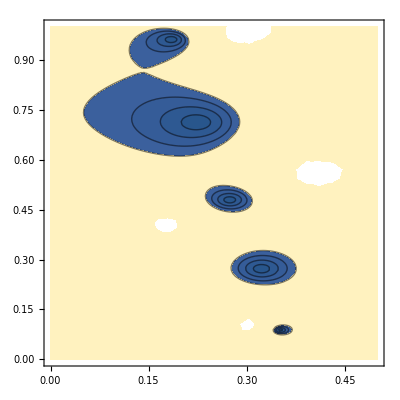

```mathematica
ContourPlot[Abs[PlotContFrac2[2,-2,-1,1/2,1,ωr-ⅈ ωi,3000,15]],{ωr,0,0.5},{ωi,0,1},Contours->{0,0.5,1,1.5,2}]
```

```mathematica
PlotModeFunction[0,-2,-1,1/2,4,1.1-ⅈ 2.1,300,15]
```

-90.1072-147.379 ⅈ

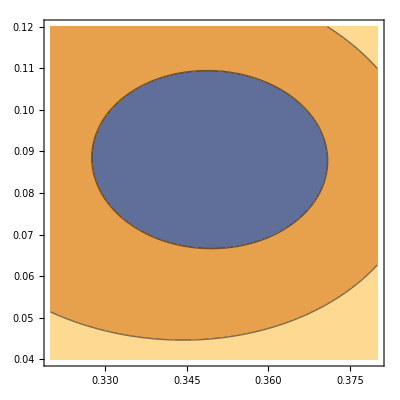

```mathematica
ContourPlot[Abs[PlotModeFunction[0,-2,-1,1/2,4,ωr-ⅈ ωi,300,15]],{ωr,0.32,0.38},{ωi,0.04,0.12},Contours->{0,0.5,1,1.5,2}]
```

```mathematica
?SetSpinWeight
```

SetSpinWeight[s] sets the value of the spin-weight used in all subsequent QNM computations:
	 s=-2 : Gravitational perturbations
	 s=-1 : Electro-Magnetic perturbations
	 s= 0 : Scalar perturbations.

```mathematica
?SchwarzschildQNM
```

SchwarzschildQNM[l,n] computes the Quasi-Normal Mode solutions for overtone n of mode l.  The mode is computed to an accuracy of 10^-14.  For given 'l', if solutions with overtones (n-1) and (n-2) have not been computed, then the routine is recersively called for overtone '(n-1).  If no solutions exist for mode l, then the first two overtones of (l-1) and (l-2) are used to extrapolate initial guesses for these modes.

Options:
	 SpinWeight→Null : -2,-1,0
		 The spin weight must be set via a call to SetSpinWeight before any KerrQNM
		 function call.
	 ModePrecision→24
	 JacobianStep→-10
		 The radial solver make use of numerical derivatives.  The relative step size
		 is set to 10^JacobianStep.
	 RadialCFMinDepth→300
		 The minimum value for the Radial Continued Fraction Depth.
	 RadialCFDepth→1
		 The initial Radial Continued Fraction Depth is usually taken from the prior 
		 solution in the sequence.  Fractional values reduce this initial value by that
		 fraction.  Integer values larger than RadialCFMinDepth are used as the new
		  initial value.
	 RadialRelax→1
		 Initial under-relaxation parameter used in Radial Newton iterations.
	 Rootϵ→-14
		 10^Rootϵ is the maximum allowed magnitude for the Radial Continued Fraction.
	 SchDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Schwarzschile iterations.
	 RadialDebug→0 : 0,1,2,3,...
		 'Verbosity' level during the Radial Newton iterations.

```mathematica
SchwarzschildQNM[2,0,RadialDebug->2]
```

OptionValue::nodef: Unknown option RadialDebug for SchwarzschildQNM.

OptionValue::optnf: Option name KerrModes`SpinWeight not found in defaults for SchwarzschildQNM.

OptionValue::nodef: Unknown option RadialDebug for SchwarzschildQNM.

OptionValue::optnf: Option name KerrModes`SpinWeight not found in defaults for SchwarzschildQNM.

```mathematica
SchwarzschildQNM[2,1]
```

Computing (l=2,n=1)

{0.346710996879163439717682-0.273914875291234817349552 ⅈ,1,300,-14,4.48374762459683541288732×10^-25}

```mathematica
SchwarzschildQNM[2,7]
```

Computing (l=2,n=2)

{0.301053454612366393018274-0.478276983223071810309085 ⅈ,2,300,-14,3.50976556069590924301404×10^-22}

Computing (l=2,n=3)

{0.251504962185592727495627-0.705148202433494339225473 ⅈ,3,300,-14,1.25435674941828175999762×10^-21}

Computing (l=2,n=4)

{0.207514579813071145491489-0.94684489086635324785649 ⅈ,4,439,-14,3.01771376343677999791552×10^-23}

Computing (l=2,n=5)

{0.169299403093045027411766-1.19560805413584790277213 ⅈ,5,723,-14,3.30382930493256220221089×10^-22}

Computing (l=2,n=6)

{0.133252340245188029172137-1.44791062616203705106769 ⅈ,6,1086,-14,3.12952152582417793221155×10^-21}

Computing (l=2,n=7)

{0.0928223336702009513531975-1.70384117220613551866982 ⅈ,7,3480,-14,2.31281200307829666370081×10^-18}

```mathematica
SchwarzschildQNM[3,0]
```

Computing (l=3,n=0)

{0.599443288437490072739494-0.0927030479449476039700741 ⅈ,0,300,-14,3.15217925795790847916052×10^-21}

```mathematica
SchwarzschildQNM[3,1]
```

Computing (l=3,n=1)

{0.582643803033299430615841-0.281298113435044044678838 ⅈ,1,300,-14,8.68558004758644884622421×10^-23}

```mathematica
SchwarzschildQNM[4,0]
```

Computing (l=4,n=0)

{0.809178377532239140693789-0.0941639609889232494057998 ⅈ,0,300,-14,1.53319546663800061559209×10^-23}

```mathematica
SchwarzschildQNM[4,1,RadialDebug->0]
```

Computing (l=4,n=1)

{0.796631532034502515160255-0.284334349404840718645842 ⅈ,1,300,-14,9.54824053299968525177899×10^-23}

```mathematica
SchwarzschildQNM[5,0]
```

Computing (l=5,n=0)

{1.0122953121353505008792-0.0948705160816095119808521 ⅈ,0,300,-14,3.06264856995914149615042×10^-21}

```mathematica
SchwarzschildQNM[5,1]
```

Computing (l=5,n=1)

{1.00222102789055837442425-0.285817381772263060312771 ⅈ,1,300,-14,7.0439156256414365508779×10^-22}

```mathematica
SchwarzschildQNM[6,4]
```

Computing (l=6,n=0)

{1.21200982065213049039679-0.0952658458420820524539497 ⅈ,0,300,-14,7.2935798708806582246754×10^-22}

Computing (l=6,n=1)

{1.20357397438875375503625-0.286649925113746968634646 ⅈ,1,300,-14,8.67574932358382723522401×10^-23}

Computing (l=6,n=2)

{1.18707367460215801956317-0.480564492780835274634178 ⅈ,2,300,-14,1.63927530443594289512448×10^-22}

Computing (l=6,n=3)

{1.16327006185105959322991-0.678590980982515134928399 ⅈ,3,300,-14,1.50673135228581770781788×10^-23}

Computing (l=6,n=4)

{1.13332410147259103240849-0.882102771131654187186261 ⅈ,4,300,-14,0}

```mathematica
?PlotSchQNM
```

PlotSchQNM[l] plots both the "positive" and "negative" frequency QNMs.  By default, the gravitational modes are plotted, but the PlotSpinWeight option can be set to change this.

Options:
	 PlotSpinWeight->-2 : -2,-1,0

PlotSchQNM also take all of the options available to ListPlot.

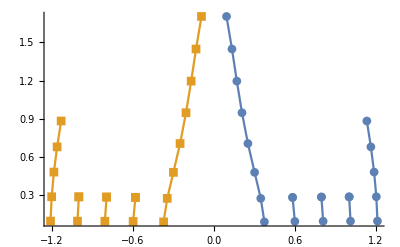

```mathematica
Show[Table[PlotSchQNM[l],{l,2,6}],PlotRange->All]
```

```mathematica
?SchQNMTable
```

Global`SchQNMTable

SchQNMTable[2]=8
 
SchQNMTable[3]=2
 
SchQNMTable[4]=2
 
SchQNMTable[5]=2
 
SchQNMTable[6]=5
 
SchQNMTable[2,0]={0.373671684418041835793492-0.0889623156889356982804609 ⅈ,0,300,-14,9.75515457051863827731063×10^-21}
 
SchQNMTable[2,1]={0.346710996879163439717682-0.273914875291234817349552 ⅈ,1,300,-14,4.48374762459683541288732×10^-25}
 
SchQNMTable[2,2]={0.301053454612366393018274-0.478276983223071810309085 ⅈ,2,300,-14,3.50976556069590924301404×10^-22}
 
SchQNMTable[2,3]={0.251504962185592727495627-0.705148202433494339225473 ⅈ,3,300,-14,1.25435674941828175999762×10^-21}
 
SchQNMTable[2,4]={0.207514579813071145491489-0.94684489086635324785649 ⅈ,4,439,-14,3.01771376343677999791552×10^-23}
 
SchQNMTable[2,5]={0.169299403093045027411766-1.19560805413584790277213 ⅈ,5,723,-14,3.30382930493256220221089×10^-22}
 
SchQNMTable[2,6]={0.133252340245188029172137-1.44791062616203705106769 ⅈ,6,1086,-14,3.12952152582417793221155×10^-21}
 
SchQNMTable[2,7]={0.0928223336702009513531975-1.70384117220613551866982 ⅈ,7,3480,-14,2.31281200307829666370081×10^-18}
 
SchQNMTable[3,0]={0.599443288437490072739494-0.0927030479449476039700741 ⅈ,0,300,-14,3.15217925795790847916052×10^-21}
 
SchQNMTable[3,1]={0.582643803033299430615841-0.281298113435044044678838 ⅈ,1,300,-14,8.68558004758644884622421×10^-23}
 
SchQNMTable[4,0]={0.809178377532239140693789-0.0941639609889232494057998 ⅈ,0,300,-14,1.53319546663800061559209×10^-23}
 
SchQNMTable[4,1]={0.796631532034502515160255-0.284334349404840718645842 ⅈ,1,300,-14,9.54824053299968525177899×10^-23}
 
SchQNMTable[5,0]={1.0122953121353505008792-0.0948705160816095119808521 ⅈ,0,300,-14,3.06264856995914149615042×10^-21}
 
SchQNMTable[5,1]={1.00222102789055837442425-0.285817381772263060312771 ⅈ,1,300,-14,7.0439156256414365508779×10^-22}
 
SchQNMTable[6,0]={1.21200982065213049039679-0.0952658458420820524539497 ⅈ,0,300,-14,7.2935798708806582246754×10^-22}
 
SchQNMTable[6,1]={1.20357397438875375503625-0.286649925113746968634646 ⅈ,1,300,-14,8.67574932358382723522401×10^-23}
 
SchQNMTable[6,2]={1.18707367460215801956317-0.480564492780835274634178 ⅈ,2,300,-14,1.63927530443594289512448×10^-22}
 
SchQNMTable[6,3]={1.16327006185105959322991-0.678590980982515134928399 ⅈ,3,300,-14,1.50673135228581770781788×10^-23}
 
SchQNMTable[6,4]={1.13332410147259103240849-0.882102771131654187186261 ⅈ,4,300,-14,0}